## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\DataVisualization\Guokr\UnAnsweredQ48

## Fetch Data

```mathematica
url[s_,e_]:=Table[StringJoin["http://www.guokr.com/ask/newest/?page=",ToString[i]],{i,s,e}]
```

```mathematica
data[s_,e_]:=Table[Import[url[s,e][[i]],"XMLObject"],{i,1,Length[url[s,e]]}]
```

```mathematica
dataRaw=data[1,50];
```

```mathematica
lenURL=Length[dataRaw]
```

50

## Processing

### Processing With The Whole list of questions

```mathematica
dataSourceTL=
Flatten[
Table[Cases[dataRaw[[i]],XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->link_},{title_}]}]:>{title,link},Infinity],
{i,1,lenURL}]
,1];
```

```mathematica
dataSourceTime=
Table[
Flatten@Cases[dataRaw[[i]],XMLElement["span",{"class"->"ask-list-time"},{time_}]:>{StringTrim[time]},Infinity]
,{i,1,lenURL}];
```

```mathematica
dataSourceQA=
Flatten[
Table[
Cases[dataRaw[[i]],XMLElement["div",{"class"->"ask-list-nums"},{temp1_,XMLElement["p",{"class"->"ask-focus-nums"},{temp2_,XMLElement["span",{"class"->"num"},{focusN_}],focusNT_}],temp3_,XMLElement["p",{"class"->"ask-answer-nums"},{temp4_,XMLElement["span",{"class"->"num"},{ansN_}],ansNT_}],temp5_}]:>{ToExpression@focusN,ToExpression@ansN},Infinity]
,{i,1,lenURL}]
,1];
```

```mathematica
dataSourceTime=
Flatten[
Table[
Flatten@Cases[dataRaw[[i]],XMLElement["span",{"class"->"ask-list-time"},{time_}]:>{StringTrim[time]},Infinity]
,{i,1,lenURL}],
1];
```

```mathematica
len=Length[dataSourceTL]
```

360

```mathematica
Length@dataSourceTime
```

360

```mathematica
Length@dataSourceQA
```

359

```mathematica
Table[Flatten@Append[Append[dataSourceTL[[i]],dataSourceQA[[i]]],dataSourceTime[[i]]],{i,1,len}]
Grid@%
```

Part::partw: Part 360 of {{3, 2}, {2, 1}, {1, 0}, {3, 3}, {7, 6}, {7, 4}, {2, 0}, {2, 2}, {1, 0}, {1, 0}, {0, 0}, {1, 0}, {1, 0}, {2, 1}, {6, 4}, {4, 1}, {2, 1}, {3, 1}, {2, 0}, {1, 0}, {12, 7}, {3, 2}, {2, 1}, {2, 1}, {1, 0}, {3, 1}, {3, 2}, {2, 1}, {1, 0}, {3, 2}, {1, 1}, {2, 1}, {4, 3}, {5, 3}, {2, 1}, {2, 2}, {1, 0}, {3, 2}, {2, 1}, {1, 1}, {2, 1}, {4, 4}, {3, 2}, {2, 1}, {2, 1}, {2, 1}, {1, 0}, {4, 3}, {2, 1}, {2, 2}, « 309 »} does not exist.

{{跳绳前脚掌着地和全脚着地对锻炼效果有影响么？双脚同时着地和两脚轮流着地对锻炼效果有影响么？,http://www.guokr.com/question/482641/,3,2,今天 11:10},{哪位生物高手帮我识别一下，这花叫什么名字呢？,http://www.guokr.com/question/482640/,2,1,今天 11:03},{怎样系统的学习植物分类？能最后做到看到植物就能想到它是什么种。我该买一本什么样的分类图鉴？,http://www.guokr.com/question/482639/,1,0,今天 11:03},{古代女子是如何化妆的？,http://www.guokr.com/question/482638/,3,3,今天 10:58},{一女同事，平时感觉彼此都很好：这堆冷笑话都是什么意思啊？,http://www.guokr.com/question/482637/,7,6,今天 10:49},{双黄蛋能孵出两只小鸡？还是只能孵出一只，或者就孵不出来了？,http://www.guokr.com/question/482636/,7,4,今天 10:45},{蚊子怎样排泄？会有便便等样的排泄物么？,http://www.guokr.com/question/482635/,2,0,今天 10:44},{能用超声波在短距离内探测地形吗？我想做个给盲人导航的装置，提醒周围的障碍物和地形。,http://www.guokr.com/question/482634/,2,2,今天 10:43},{长时间低头玩手机会长出双下巴吗？,http://www.guokr.com/question/482631/,1,0,今天 10:35},{在微博上看的的这些问题，好想知道。,http://www.guokr.com/question/482630/,1,0,今天 10:33},{波音777的油箱在上部？,http://www.guokr.com/question/482629/,0,0,今天 10:32},{写字楼还有公寓楼，以个人名义或公司名义购买有什么政策区别和后期的政策区别,http://www.guokr.com/question/482628/,1,0,今天 10:32},{一些粉状的食物比如奶粉，受潮了就一定会变质吗？,http://www.guokr.com/question/482627/,1,0,今天 10:27},{猫咪的爪子肌肉和骨骼结构是什么样的，为什么能收能放？,http://www.guokr.com/question/482626/,2,1,今天 10:25},{天气好闷热啊，想知道古时候皇上帝王如何消暑？有冰棍吃吗？没空调怎么过啊？,http://www.guokr.com/question/482625/,6,4,今天 10:21},{浪花发出蓝色荧光是怎么回事？,http://www.guokr.com/question/482623/,4,1,今天 10:20},{强噪音环境下，用耳罩式耳机听乐音能不能抵消噪声危害？,http://www.guokr.com/question/482622/,2,1,今天 10:17},{卫生棉条和卫生巾哪个更卫生，更健康，各自的优缺点都是什么？传说长期使用卫生棉条容易造成子宫内膜异位，是真的吗？女性吸烟与月经不调、痛经有关吗？求大神~~~~~,http://www.guokr.com/question/482621/,3,1,今天 10:17},{在药店买的干菊花回来泡菊花茶喝，但是经常会有些黑色的小虫子，又一次泡开还看到类似蠕虫的东西了，但是在网上搜了一下很多人都遇到过这个现象，想问问原因，这种菊花还能泡茶喝吗？,http://www.guokr.com/question/482620/,2,0,今天 10:12},{奶粉罐封口处铝箔鼓起是什么原因？,http://www.guokr.com/question/482619/,1,0,今天 10:09},{男生从早到晚穿着游泳裤会有什么健康问题吗？,http://www.guokr.com/question/482618/,12,7,今天 10:03},{最近看到同事的一套房格局不是很理想，卧室处于整个建筑凹进去的那部分。为什么开发商当时不把楼盖成个矩形的，非要在这个地方留个凹口，弄得户型不尴不尬的...所以想问问大侠们，开发商这么做得原因是啥？,http://www.guokr.com/question/482614/,3,2,今天 09:58},{为什么竖线条很密集的时候会有波浪形的花纹感觉？,http://www.guokr.com/question/482606/,2,1,今天 09:51},{一个小问题：人类是不是目前发现的唯一会避孕的生物？还发现了其他物种会避孕么？,http://www.guokr.com/question/482602/,2,1,今天 09:45},{铁血战士的隐身系统怎么做到隐身的？现在的科技能做出来吗？,http://www.guokr.com/question/482596/,1,0,今天 09:41},{是否存在一个带密码的zip/rar文件，给予两个不同的密码可以解压出两个不同的文件？,http://www.guokr.com/question/482594/,3,1,今天 09:33},{为什么打针的时候不疼，出门一分钟后却开始疼？,http://www.guokr.com/question/482593/,3,2,今天 09:30},{是否可以在汽车底部设置一块橡胶板，在最紧急的急刹车的时候触地，增加摩擦力，缩短刹车距离，防止追尾。,http://www.guokr.com/question/482592/,2,1,今天 09:22},{庄淑旗这个人到底是不是博士？说的坐月子的方法有用吗？,http://www.guokr.com/question/482591/,1,0,今天 09:18},{MATLAB等专业软件能否在MAC OS上运行？ 如果不想在MAC上刷成瘟斗士有可能么？,http://www.guokr.com/question/482590/,3,2,今天 08:55},{人体以肚脐为圆心做圆周运动（可以是360度立体旋转的）。当人达到哪个角度时人最恐惧？,http://www.guokr.com/question/482589/,1,1,今天 08:47},{求鉴定这种虫子的名称以及杀灭的方法,http://www.guokr.com/question/482588/,2,1,今天 08:30},{人生病的时候，比如扁桃体发炎、感冒或者尿道炎等等发生的时候，医生一般都说不能吃辛辣的食物，那么那些生来吃辣的的四川人，湖南人，还有吃咖喱的印度人生病的时候怎么办，他们都是吃辣的呀？,http://www.guokr.com/question/482587/,4,3,今天 08:27},{求解释。医学研究证明,仰卧起坐对腹部脂肪并无特别效用。储存脂肪的细胞和肌肉细胞具有完全不同特性,两者不能互相转换。因此仰卧起坐虽可锻炼腹部肌肉,练出肌肉线条,但对消除腹部脂肪,并不比其他运动更有效。,http://www.guokr.com/question/482586/,5,3,今天 07:46},{为什么美国麦当劳肯德基汉堡用牛肉饼而中国用炸鸡，是因为成本更低吗？,http://www.guokr.com/question/482585/,2,1,今天 07:45},{信用卡是如何被盗刷的? .,http://www.guokr.com/question/482584/,2,2,今天 07:34},{设计文具纸质笔记本需要学什么基础么？,http://www.guokr.com/question/482583/,1,0,今天 07:30},{为什么人摔伤了会青或紫？,http://www.guokr.com/question/482582/,3,2,今天 07:10},{为什么吸油纸比普通纸更吸油？,http://www.guokr.com/question/482581/,2,1,今天 07:09},{世界上第一个钟表是根据什么校时的？,http://www.guokr.com/question/482580/,1,1,今天 07:06},{原子空心，何以构成实心物体？原子百分之九十九以上的体积是空的，但是原子构成的铁锤看起来却是实心的。二者看似矛盾，为什么？,http://www.guokr.com/question/482579/,2,1,今天 05:10},{月经为什么一个月一经？,http://www.guokr.com/question/482578/,4,4,今天 04:36},{淘宝怎么注册   很麻烦。,http://www.guokr.com/question/482577/,3,2,今天 04:35},{有沒有對上火這件事情做過研究啊，到底上火對應什麼症狀呢？,http://www.guokr.com/question/482576/,2,1,今天 04:04},{为什么好多人喜欢重操旧业？,http://www.guokr.com/question/482563/,2,1,今天 01:45},{二郎神第三只眼会不会长眼睫毛？如果有的话会怎么长？,http://www.guokr.com/question/482561/,2,1,今天 01:20},{龙卷风的等级是怎么划分的？,http://www.guokr.com/question/482560/,1,0,今天 01:00},{重复写某个字会觉得奇怪？,http://www.guokr.com/question/482559/,4,3,今天 00:58},{抗日战场上有“炮弹休克症”么？,http://www.guokr.com/question/482556/,2,1,今天 00:38},{大家对未来教室有什么看法和想法,http://www.guokr.com/question/482553/,2,2,今天 00:23},{求比较快的NRL Tropical Cyclone Page 的URL,http://www.guokr.com/question/482552/,1,0,今天 00:21},{什么是智商？如何衡量一个人的智商？,http://www.guokr.com/question/482551/,2,1,今天 00:20},{蟑螂吃人的胡子吗？,http://www.guokr.com/question/482549/,2,1,今天 00:19},{现代战争中，我们如何逃跑啊？怎么才能高速度的逃跑？,http://www.guokr.com/question/482544/,3,2,今天 00:11},{女人是食指比无名指长，男人则相反，是这样吗？,http://www.guokr.com/question/482530/,2,2,2013-07-07 23:59},{有哪种荷尔蒙分泌是会加速入眠么？,http://www.guokr.com/question/482527/,2,2,2013-07-07 23:55},{给小学生教一些科学知识，大家觉得教什么比较好？让他们比较容易接受，又有启发意义呢？谢谢大家啦~,http://www.guokr.com/question/482526/,1,0,2013-07-07 23:38},{在沙漠大规模铺设光伏，可以减少蒸发量，是否可能改变沙漠气候，导致消灭沙漠？,http://www.guokr.com/question/482525/,2,1,2013-07-07 23:38},{苏丹式躺椅(BarcaLounger)是什么？,http://www.guokr.com/question/482524/,2,1,2013-07-07 23:34},{到国外转机，价格能便宜一半以上。这是为什么呢？ 上海-旧金山航线最低1.3万，韩国转机则是6千多。,http://www.guokr.com/question/482523/,5,1,2013-07-07 23:31},{在C语言中，仅给出两个变量，如int a=10,b=20;在不使用其他变量的情况下，能将a,b的值交换吗？？？,http://www.guokr.com/question/482520/,3,2,2013-07-07 23:17},{神农架修机场真的会破坏生态吗？削山峰、填溶洞确实对环境有影响吗？,http://www.guokr.com/question/482517/,2,1,2013-07-07 23:06},{携带狂犬病毒的狗的精子会携带狂犬病毒吗?狂犬病毒由母亲传播给子女？,http://www.guokr.com/question/482516/,1,0,2013-07-07 23:03},{为什么泡泡有时可以让手指穿过却不破？,http://www.guokr.com/question/482515/,3,1,2013-07-07 23:00},{哭泣是“人类特有的表达方式”吗？ “动物会哭”目前是不是没有切实佐证？,http://www.guokr.com/question/482514/,2,0,2013-07-07 22:57},{载人火箭为什么不在“箭管”里发射？,http://www.guokr.com/question/482513/,4,3,2013-07-07 22:51},{为什么天气预报里说北京7月10日最低温度零下7度呢？ 这是怎么回事？,http://www.guokr.com/question/482512/,3,1,2013-07-07 22:49},{什么样的液体才具有不可压缩性？,http://www.guokr.com/question/482511/,2,1,2013-07-07 22:43},{朋友结婚说什么祝福话？,http://www.guokr.com/question/482510/,3,2,2013-07-07 22:30},{上市对一个公司来说究竟有哪些好处？,http://www.guokr.com/question/482509/,3,2,2013-07-07 22:30},{"暴晒后的矿泉水会发生材质软化，释放有毒物质到水里，千万别喝"，这个说法正确吗？,http://www.guokr.com/question/482508/,4,3,2013-07-07 22:21},{我比女盆友高出30cm，我怎么吻她啊？初吻，没经验，求详细教程~挑战好大！,http://www.guokr.com/question/482507/,2,1,2013-07-07 22:14},{大家都是穿布裤的时候会凸显下面的吗？,http://www.guokr.com/question/482506/,1,0,2013-07-07 22:13},{【男默女泪向】我要学护理，谁来劝劝我。,http://www.guokr.com/question/482505/,2,1,2013-07-07 22:10},{     狗狗携带狂犬病毒的几率有多大？,http://www.guokr.com/question/482504/,1,0,2013-07-07 22:09},{请问常见的蜻蜓都都那些种  今天见到只粉红色蜻蜓 比常见蜻蜓小 很漂亮,http://www.guokr.com/question/482503/,2,0,2013-07-07 22:07},{请问正确的读书姿势是什么样的。可以保护颈椎的
,http://www.guokr.com/question/482502/,1,0,2013-07-07 22:05},{如果一个人不小心吞咽了狂犬病毒那么感染狂犬病的几率有多大?如果正处于发病期间的患狂犬病的狗不是直接舔到伤口，而是舔到其他身体或其他物品再由身体或其他物品传播到伤口病使病毒进入体内的可能性有多大？,http://www.guokr.com/question/482501/,1,0,2013-07-07 22:01},{如果体内已经携带狂犬病毒并没有发病的狗然后再接种狂犬疫苗能起到什么作用？还有没有必要？如果一个人不小心吞咽了狂犬病毒有多少几率会感染狂犬病？,http://www.guokr.com/question/482500/,1,0,2013-07-07 21:52},{黄帝和炎帝与三纲五常的关系是什么？＜商君书•画册＞中＂黄帝作君臣上下之义，父子兄弟之礼，夫妇匹配之合，内行刀锯，外用甲兵＂可以理解为三纲五常的体现吗？,http://www.guokr.com/question/482499/,1,0,2013-07-07 21:52},{如果体内已经携带狂犬病毒并没有发病的狗然后再接种狂犬疫苗能起到什么作用？还有没有必要？如果一个人不小心吞咽了狂犬病毒有多少几率会感染狂犬病？,http://www.guokr.com/question/482500/,1,0,2013-07-07 21:52},{黄帝和炎帝与三纲五常的关系是什么？＜商君书•画册＞中＂黄帝作君臣上下之义，父子兄弟之礼，夫妇匹配之合，内行刀锯，外用甲兵＂可以理解为三纲五常的体现吗？,http://www.guokr.com/question/482499/,1,0,2013-07-07 21:52},{什么条件下宏观物质在微观下呈晶体结构？,http://www.guokr.com/question/482498/,1,0,2013-07-07 21:50},{金字塔的砖几无空隙，刀片插不进去，有没有可能是因为砖与砖发生了扩散现象？,http://www.guokr.com/question/482497/,1,0,2013-07-07 21:42},{孙子定理是什么？有通俗的解释吗？,http://www.guokr.com/question/482496/,1,0,2013-07-07 21:36},{打败仗为什么叫“败北”呢？,http://www.guokr.com/question/482495/,2,2,2013-07-07 21:35},{为什么十二生肖里没有猫呢？,http://www.guokr.com/question/482494/,2,2,2013-07-07 21:31},{不可定义数是真是假？,http://www.guokr.com/question/482493/,3,1,2013-07-07 21:24},{一吨反物质能把地球炸掉吗？,http://www.guokr.com/question/482492/,1,0,2013-07-07 21:20},{为什么超人钢铁之躯这么2.就看见两个傻逼超人撞来撞去，最后脖子一勒就死了，氪星就要毁灭了，为什么还把那些超人发送到外太空，太便宜他们了吧。,http://www.guokr.com/question/482490/,2,1,2013-07-07 21:19},{整形医生鼓吹的＂光子美容＂原理是什么？真的靠谱吗？,http://www.guokr.com/question/482487/,1,0,2013-07-07 21:04},{小鸟为什么喜欢一只脚站立？,http://www.guokr.com/question/482485/,3,1,2013-07-07 20:47},{为什么有时候不是蚊子叮，大腿或是其他地方会有被蚊子叮似的轻微疼痛感呢？是幻觉还是蚊子叮了又跑了？,http://www.guokr.com/question/482484/,2,1,2013-07-07 20:46},{看了这个视频，我想问，光子真的是运动的吗。,http://www.guokr.com/question/482483/,1,0,2013-07-07 20:44},{有谁会制作小羊肖恩的公仔？,http://www.guokr.com/question/482482/,1,0,2013-07-07 20:35},{纯蜂蜜不会变质对不对？,http://www.guokr.com/question/482481/,3,2,2013-07-07 20:31},{百合里散发出的生物碱会让人心肌变脆弱，让人在睡梦中死去，这科学吗？,http://www.guokr.com/question/482480/,1,0,2013-07-07 20:15},{耳朵如何辨别不同声音？,http://www.guokr.com/question/482479/,1,0,2013-07-07 20:05},{为什么羽毛球落下时是旋转的?,http://www.guokr.com/question/482478/,1,0,2013-07-07 20:05},{西瓜那半边好吃？,http://www.guokr.com/question/482477/,2,1,2013-07-07 19:42},{人是否只能记得曾经的感官感受，如记得疼痛过，但过后却忘记该感受的程度？就是忘记了有多痛。
,http://www.guokr.com/question/482476/,2,1,2013-07-07 19:36},{本拉登— 他出身大户门第，身价数十亿，本应是娶女星玩模特的年纪，但是为了自己的信仰，他把数十亿换成了AK47和RPG，钻进了山洞对抗美帝主义，十年来让FBI和CIA颜面扫地
这是真实的本拉登么？求教,http://www.guokr.com/question/482475/,1,0,2013-07-07 19:33},{今天，辽宁省某地，捡到一只雏鸟，不知什么品种，请大家鉴别,http://www.guokr.com/question/482474/,4,3,2013-07-07 19:31},{看到《死亡笔记》里面将埃博拉与感冒融合成一个新病毒，这事儿可能成功么？如果成功了有与感冒相当的传染力与埃博拉的致病力么？,http://www.guokr.com/question/482473/,3,3,2013-07-07 19:27},{牛奶变酸奶后，体积和质量会发生变化吗？,http://www.guokr.com/question/482472/,1,0,2013-07-07 19:15},{书到今生读已迟在网上流传的故事真的假的,http://www.guokr.com/question/482470/,2,2,2013-07-07 19:07},{linux不是嵌入系统吗，那么黑莓能不能刷？,http://www.guokr.com/question/482468/,2,2,2013-07-07 18:55},{在不影响长个子没有健身器材的情况下怎样练出腹肌和胸肌？我17岁,http://www.guokr.com/question/482461/,1,0,2013-07-07 18:48},{什么是好的产品体验？,http://www.guokr.com/question/482460/,1,0,2013-07-07 18:47},{力矩是什么？为什么矢径与作用力的矢量积即力矩？,http://www.guokr.com/question/482442/,3,2,2013-07-07 18:23},{话说前段时间在流言终结者里看到一个流言，貌似是说中世纪的一种酷刑，就是把人仰面绑在椅子上，在额头的位置放一个滴水装置，不停地向那人额头上滴水。一段时间后那个人貌似会疯掉。真的会这样吗？,http://www.guokr.com/question/482441/,1,0,2013-07-07 18:19},{请问这是蝴蝶还是飞蛾或是其他？,http://www.guokr.com/question/482440/,4,3,2013-07-07 18:19},{胶版印刷中的UV对人体有什么危害？UV灯以及UV油墨，为什么在经过灯照射后会有很大的异味产生，那气体是什么？对人体有害么？,http://www.guokr.com/question/482439/,2,1,2013-07-07 18:17},{上一点档次的地方为什么都用男性迎宾？,http://www.guokr.com/question/482438/,1,1,2013-07-07 18:12},{同一面墙上的一个大窗子跟两扇面积加起来跟大窗子一样大的小窗子哪一个通风效率比较高？,http://www.guokr.com/question/482437/,2,1,2013-07-07 18:10},{为什么船边会有小孔往外流水呢？,http://www.guokr.com/question/482436/,2,1,2013-07-07 18:08},{古代弓箭手到底怎样作战？,http://www.guokr.com/question/482435/,1,0,2013-07-07 18:07},{我很喜欢看帅哥，但帅哥一换发型或衣服我就不太认得了，老以为是另一帅哥，这是为啥？,http://www.guokr.com/question/482434/,2,1,2013-07-07 18:00},{盐蒸橙子真的能治咳嗽吗?,http://www.guokr.com/question/482433/,3,2,2013-07-07 17:55},{真有这么牛的草？血癌、末期肿瘤啊，用此神草就都治愈了？,http://www.guokr.com/question/482432/,3,3,2013-07-07 17:49},{人真的会吓尿吗？,http://www.guokr.com/question/482431/,5,4,2013-07-07 17:44},{为什么我的精液一部分是透明液体，一部分是白色偏淡黄色的液体？,http://www.guokr.com/question/482430/,1,0,2013-07-07 17:44},{可以同时看见闪电 听见雷声吗? ,http://www.guokr.com/question/482429/,1,1,2013-07-07 17:42},{关于C语言的指针与数据结构的问题



,http://www.guokr.com/question/482428/,1,0,2013-07-07 17:37},{请问这是蝴蝶还是飞蛾？,http://www.guokr.com/question/482427/,1,0,2013-07-07 17:31},{KFC的两个甜筒的冰激凌多还是一个圣代的多？,http://www.guokr.com/question/482426/,3,2,2013-07-07 17:30},{国家严抓三公消费，曾靠单位招待的酒店，现今如何转型？,http://www.guokr.com/question/482425/,3,2,2013-07-07 17:27},{人类行进距离与能量,http://www.guokr.com/question/482424/,2,1,2013-07-07 17:26},{为什么马化腾总是被人骂？,http://www.guokr.com/question/482423/,2,1,2013-07-07 17:25},{为什么下载工具在下载文件的时候一般都会产生2个临时的文件？,http://www.guokr.com/question/482422/,2,1,2013-07-07 17:24},{前段时间去西藏，从觉巴山（左贡县境内）过时，就在路边看到一个野生动物，不知道是什么动物，有没有人知道？,http://www.guokr.com/question/482421/,4,3,2013-07-07 17:17},{我现在高二，数学和物理不错，但我先天弱视，现在已经850度了，以后选什么专业比较合适。求各位给个建议，谢谢,http://www.guokr.com/question/482420/,1,1,2013-07-07 17:13},{捡了一只大拇指甲盖那样大的蜗牛，但是不知道他吃什么，就随便塞了几根草,http://www.guokr.com/question/482419/,2,1,2013-07-07 17:12},{这个问题和人的眼睛有关，首先你要闭上双眼，然后用一根手指轻轻按压眼眶的一边，同时你的眼球向手指按压的对面那一边看去，你会发现一个黄色的类似瞳孔一样的东西，谁知道这是怎么回事儿呢？,http://www.guokr.com/question/482418/,2,1,2013-07-07 17:05},{植物鉴定：这是什么花呢？红色的花和带白点的叶子,http://www.guokr.com/question/482417/,2,1,2013-07-07 17:05},{后背发冷在生理上怎么解释？,http://www.guokr.com/question/482416/,3,1,2013-07-07 16:57},{无线路由的疑问,http://www.guokr.com/question/482415/,2,1,2013-07-07 16:54},{硅藻是怎么形成含硅外壳的？,http://www.guokr.com/question/482414/,2,0,2013-07-07 16:40},{老人说吃生猪肉会得癫痫，那古代人吃野猪肉呢？有没有什么案例证明？,http://www.guokr.com/question/482413/,4,3,2013-07-07 16:40},{除了跑步和吃减肥药还有更好的减肥方法吗？,http://www.guokr.com/question/482411/,3,2,2013-07-07 16:32},{不知道大家是不是和我一样，在每天起床后大约10多分钟内，身体相比平常弯曲程度更小，或者说身体很僵硬，特别是脊髓骨一条感觉明显，为什么会这样？？？求大神解答？？？,http://www.guokr.com/question/482410/,2,1,2013-07-07 16:19},{临床大二，不太读得下去了，转专业？临床or生科？
  
,http://www.guokr.com/question/482409/,1,0,2013-07-07 16:18},{我是纯合子。请问纯合子在人群中的比例大概是多少？什么情况下会出现纯合子？在遗传上又有什么优势和劣势？,http://www.guokr.com/question/482408/,2,2,2013-07-07 16:15},{乡道为什么是Y开头的？,http://www.guokr.com/question/482407/,2,1,2013-07-07 15:37},{ A在大钟里，B在外面使劲敲钟，没想到把自己给震得很难受，在里面的A反倒若无其事，为什么？,http://www.guokr.com/question/482406/,2,2,2013-07-07 15:36},{Ｎ以内相邻素数最大间距的猜想,http://www.guokr.com/question/482405/,1,2,2013-07-07 15:36},{三维立体画的原理是什么？如何制作三维立体画？,http://www.guokr.com/question/482404/,1,0,2013-07-07 15:33},{我是个高中生，大学我想念历史系，不知道哪些学校比较好，也不要特别好的学校，刚够一本的那种最好，学校最好在气候神马都好点的地方。  另，如果想留校做老师的话，是不是一定得考博士啊，硕士行不行呢？,http://www.guokr.com/question/482403/,1,0,2013-07-07 15:29},{脚气和足廯有区别吗？,http://www.guokr.com/question/482402/,3,2,2013-07-07 15:22},{出了汗再涂花露水为什么感觉比直接涂更加清凉？,http://www.guokr.com/question/482401/,3,2,2013-07-07 15:21},{袋装牛奶或酸奶的包装袋的印刷油墨都会掉色，尤其着水以后（水溶性油墨？），这些油墨会不会对健康威胁很大,http://www.guokr.com/question/482400/,1,0,2013-07-07 15:16},{赛车尾部喷火是怎么回事？
看赛车节目和电影时，有时候看到车子一加速的时候，尾部排气管会喷火，具体是什么情况？,http://www.guokr.com/question/482399/,1,0,2013-07-07 15:16},{意志能否带来超出物质的力量？,http://www.guokr.com/question/482397/,2,1,2013-07-07 15:12},{香港哪里有工程类英文书店，请大家推荐一下,http://www.guokr.com/question/482396/,1,0,2013-07-07 15:08},{电视火山泥是真的吗？,http://www.guokr.com/question/482395/,1,0,2013-07-07 14:58},{我想问一下，有没有那种“恐惧人类”的精神病，历史上有实际案例吗，他们的一生是怎么过的？,http://www.guokr.com/question/482394/,3,2,2013-07-07 14:47},{为什么我在优酷上面有好多字体呢？这个www.xinmengshi.com这个东西是怎么弄在视频上的啊，求解啊?想学习啊,http://www.guokr.com/question/482393/,2,1,2013-07-07 14:46},{为什么航模直升机采用贝尔-希拉控制系统，而真机不采用这种控制系统？,http://www.guokr.com/question/482392/,3,2,2013-07-07 14:40},{注射用的麻醉药口服也能起效吗？药效会打折扣吗？,http://www.guokr.com/question/482391/,2,0,2013-07-07 14:24},{火焰山是不是丹霞地貌？,http://www.guokr.com/question/482390/,1,0,2013-07-07 14:19},{怎样评价恩格斯（有人说他才是修正主义的鼻祖)

,http://www.guokr.com/question/482389/,1,0,2013-07-07 14:19},{上海崇明岛是不是经济很发达，为什么那里土地划分很均匀！！,http://www.guokr.com/question/482388/,1,0,2013-07-07 14:18},{用激光笔“注视”摄像头，能令其发生一过性“失明”吗？还是永久性失明？,http://www.guokr.com/question/482387/,2,1,2013-07-07 14:18},{是不是房间内湿度越大，空调的制冷效率越高？,http://www.guokr.com/question/482386/,1,0,2013-07-07 14:02},{文科生学习电气工程及自动化专业需要做那些准备？,http://www.guokr.com/question/482379/,1,0,2013-07-07 13:32},{扭动脖子，使其发出爆裂声（如同按动手指发出的声音一样）做这样的动作对脖子有什么伤害，亦或者没伤害,http://www.guokr.com/question/482378/,3,1,2013-07-07 13:29},{为什么光的色散可以散出不同的色光出来? 究竟是什么原理才会产生不同的色光?,http://www.guokr.com/question/482377/,2,1,2013-07-07 13:27},{从进化的角度上来说，哺乳动物和鸟类的关系是什么？有高等低等之分吗？,http://www.guokr.com/question/482376/,2,1,2013-07-07 13:26},{早上在公园看见一只蜻蜓，仔细一看发现与平日所见有所不同，头部有一对触角。请问是怎样造成的？,http://www.guokr.com/question/482375/,3,2,2013-07-07 13:24},{为什么以光速运动就有可能时间倒流?时间膨胀又是什么意思?,http://www.guokr.com/question/482374/,4,3,2013-07-07 13:24},{如果我们的太阳光辉一下子熄灭了，或者说抵达地球的阳光被巨大的障碍物遮挡了，地球会怎样？,http://www.guokr.com/question/482373/,3,3,2013-07-07 13:21},{我一个同学被主管骂了之后失去判断能力是怎么回事？跪求回答者！,http://www.guokr.com/question/482372/,3,3,2013-07-07 13:09},{捅人二十刀依旧是轻伤?知识的力量！,http://www.guokr.com/question/482371/,2,1,2013-07-07 12:52},{为什么洗澡后卫生间总是会比外面更热？,http://www.guokr.com/question/482370/,4,4,2013-07-07 12:42},{印第安人的起源，是从亚洲过去的吗？,http://www.guokr.com/question/482369/,3,2,2013-07-07 12:37},{为什么犹太人在二战期间以及之前受过那么多迫害从来没有大规模的反抗。以犹太人的智慧和能力我想这不是什么大问题吧。,http://www.guokr.com/question/482368/,2,1,2013-07-07 12:32},{“有限个正态分布的线性组合仍然是正态分布”的逆否命题是“（子样本线性组合而构成的）总体样本不是正态分布，则子样本不全部是正态分布”吗？逆否命题是真是假？,http://www.guokr.com/question/482367/,1,0,2013-07-07 12:26},{请高手通俗地解释一下meta-narrative!,http://www.guokr.com/question/482366/,2,1,2013-07-07 12:25},{关于在大学期间女生寝室矛盾问问题。,http://www.guokr.com/question/482365/,1,0,2013-07-07 12:21},{喜欢一个人就要说出来吗？,http://www.guokr.com/question/482364/,1,0,2013-07-07 12:09},{怎么使重叠的螺旋桨产生的风力更大？要同向还是逆向？,http://www.guokr.com/question/482361/,1,0,2013-07-07 11:32},{如何把医用酒精纯化？,http://www.guokr.com/question/482359/,4,3,2013-07-07 11:15},{在Wi-Fi环境中，同时上网的设备越多上网越慢吗？,http://www.guokr.com/question/482358/,5,4,2013-07-07 11:15},{人眼能识别的帧数最高是多少？,http://www.guokr.com/question/482357/,1,0,2013-07-07 11:04},{这个可怜的鸡蛋要怎么出来？,http://www.guokr.com/question/482356/,1,1,2013-07-07 11:02},{口腔中脱落的上皮细胞大部分是死的，为什么还可以用来测DNA呢？是不是有些链并没有断？,http://www.guokr.com/question/482355/,3,2,2013-07-07 10:58},{开整夜空调，和门窗紧闭中途被闷热弄醒，哪个更伤身体？,http://www.guokr.com/question/482354/,3,2,2013-07-07 10:58},{遇到哪些火爆啰嗦的家人该怎么办？,http://www.guokr.com/question/482353/,1,0,2013-07-07 10:45},{贴墙真的可以长高吗？,http://www.guokr.com/question/482352/,2,1,2013-07-07 10:44},{古代贵族、妃子的封号怎样翻译给外国人呢？,http://www.guokr.com/question/482351/,8,5,2013-07-07 10:42},{如果地球上只剩一男一女两个人，还能不能繁衍出一个文明来？,http://www.guokr.com/question/482350/,5,4,2013-07-07 10:35},{为什么有的人打嗝声音很大，而有的人很小？,http://www.guokr.com/question/482349/,1,0,2013-07-07 10:32},{为什么ABS塑料使用几年后会发黄,http://www.guokr.com/question/482348/,2,1,2013-07-07 10:29},{请爱车和了解的人士帮忙推荐几款私家车，购买时应注重车的那些性能以及性价比！！！！,http://www.guokr.com/question/482347/,1,0,2013-07-07 10:28},{y=1是幂函数么？网上答案各种不一样,http://www.guokr.com/question/482346/,2,2,2013-07-07 10:22},{请问现在法律界怎么判断音乐抄袭？,http://www.guokr.com/question/482345/,3,2,2013-07-07 10:20},{怎样抄东西比较快？,http://www.guokr.com/question/482344/,5,4,2013-07-07 10:07},{在历史上，飞机在降落时曾经出现过哪些故障？,http://www.guokr.com/question/482343/,1,1,2013-07-07 10:03},{蚊子和苍蝇哪个飞得快？,http://www.guokr.com/question/482342/,2,1,2013-07-07 09:56},{如果不达到第一宇宙速度,而是像爬梯子一样一点一点垂直向上缓慢移动,能不能脱离地球轨道呢?,http://www.guokr.com/question/482341/,5,4,2013-07-07 09:54},{蚊子和苍蝇哪个飞得快？,http://www.guokr.com/question/482342/,2,1,2013-07-07 09:56},{如果不达到第一宇宙速度,而是像爬梯子一样一点一点垂直向上缓慢移动,能不能脱离地球轨道呢?,http://www.guokr.com/question/482341/,5,4,2013-07-07 09:54},{硬盘的重量会随着硬盘里的信息多少而增加吗？,http://www.guokr.com/question/482340/,4,3,2013-07-07 09:04},{长河落日圆有啥科学道理么？？的确是圆的。,http://www.guokr.com/question/482339/,1,0,2013-07-07 09:00},{坐飞机的时候尾部是不是不安全？今天早上看新闻，韩亚航空的777尾巴掉下来了！！,http://www.guokr.com/question/482338/,2,1,2013-07-07 08:48},{在中国用的手机，可以在国外用吗？,http://www.guokr.com/question/482337/,3,2,2013-07-07 08:30},{这个大虫子是蟑螂么，和常见蟑螂有什么不同？,http://www.guokr.com/question/482336/,8,9,2013-07-07 08:30},{吸入福尔马林会头晕吗？会有什么反应？,http://www.guokr.com/question/482335/,5,4,2013-07-07 08:29},{塑胶模型玩具（动画人物，小猫小狗之类）的工业批量制造过程中是如何精准上色的？,http://www.guokr.com/question/482334/,2,1,2013-07-07 08:02},{这货是个啥龟？俺平时喂它面条和馍，还有生白菜叶子，这货虽然也吃，但不晓得是不是该它吃的东西。,http://www.guokr.com/question/482333/,5,4,2013-07-07 07:30},{脱脂牛奶是怎么脱脂的？,http://www.guokr.com/question/482332/,4,1,2013-07-07 07:25},{怎么样伤口才能好的快？,http://www.guokr.com/question/482331/,2,1,2013-07-07 07:18},{猫为什么给人优雅的印象？这种印象是跨文化存在的吗？,http://www.guokr.com/question/482330/,5,4,2013-07-07 06:25},{本人学生党，自高中懂男女关系以来，到即将进入大二一直没有谈过恋爱，这一次，,http://www.guokr.com/question/482329/,2,2,2013-07-07 05:50},{为什么会有庞加莱重现时间？求达人解释,http://www.guokr.com/question/482328/,3,2,2013-07-07 04:21},{你讨厌自己的父母吗?,http://www.guokr.com/question/482327/,5,3,2013-07-07 04:15},{由于地球的运动，穿时间会不会一下到太空？绝对空间不是存在么？,http://www.guokr.com/question/482326/,3,2,2013-07-07 03:57},{超高速摄影中的存储是如何实现的？使用什么样的介质？如何解决数据传输、缓存等的问题？极快快门速度下的进光量如何保证？,http://www.guokr.com/question/482325/,4,3,2013-07-07 03:13},{好恐怖.这是什么啊?,http://www.guokr.com/question/482323/,2,1,2013-07-07 02:45},{防弹衣有几种？分别有几层？是有什么材料做成的？,http://www.guokr.com/question/482317/,1,0,2013-07-07 02:14},{有人像我一样因为看不出立体图而怀疑自己没右脑的么！！别人能看出来自己看不出真的好抓狂啊！！！,http://www.guokr.com/question/482316/,2,1,2013-07-07 02:08},{孔子被联合国教科文组织评为世界十大文化名人之首是真的吗？,http://www.guokr.com/question/482315/,1,0,2013-07-07 02:03},{元素周期表第117号元素，根据爱因斯坦相对论不符合元素周期律，是否元素周期律被打破？,http://www.guokr.com/question/482314/,3,2,2013-07-07 01:59},{处女不一定会流血？真的假的,http://www.guokr.com/question/482313/,4,3,2013-07-07 01:11},{如何提高人的自控能力？,http://www.guokr.com/question/482312/,4,3,2013-07-07 01:00},{床上有蜈蚣怎么办？,http://www.guokr.com/question/482311/,5,3,2013-07-07 00:53},{浏览器打开网页却显示下图,这是什么情况呀?,http://www.guokr.com/question/482310/,3,2,2013-07-07 00:38},{科学到底有没有永恒的真理？,http://www.guokr.com/question/482309/,2,1,2013-07-07 00:35},{突然想问钢铁侠的推进工质最有可能是什么？,http://www.guokr.com/question/482308/,3,2,2013-07-07 00:24},{http://gx.legaldaily.com.cn/content/2013-07/05/content_4620505.htm
这个毒物到底是什么？,http://www.guokr.com/question/482307/,2,1,2013-07-07 00:23},{为什么有些方言用汉语拼音拼不出来？方言里的声调和普通话也不一样，方言要怎么准确的记录下来读音？,http://www.guokr.com/question/482305/,3,2,2013-07-07 00:19},{关于电信光纤、itv、光猫设置,http://www.guokr.com/question/482300/,2,1,2013-07-07 00:01},{为什么就睡不着觉呢？？从出生到2012年我一直都是晚上10点肯定会进入睡眠，而且睡眠质量一直很好，可是现在晚上睡不着白天睡不醒。,http://www.guokr.com/question/482298/,1,0,2013-07-06 23:45},{大便很疼，长时间用凡士林润滑后排便有害处吗？,http://www.guokr.com/question/482297/,4,2,2013-07-06 23:45},{为什么许多人家里都有过一条这样的床单！,http://www.guokr.com/question/482296/,5,3,2013-07-06 23:44},{眉毛有什么用，总不会只是为了好看在进化中没被淘汰吧？,http://www.guokr.com/question/482295/,4,2,2013-07-06 23:42},{风化壳包含土壤和残积物？这个观点对吗？残积物与风化壳形成一组对比的（二元结构那个），风化壳可否算成是一种成土母质类型？,http://www.guokr.com/question/482294/,1,0,2013-07-06 23:39},{有什么方法可以提高穿针的速度啊！,http://www.guokr.com/question/482293/,3,3,2013-07-06 23:27},{果壳，跟百度知道是什么关系？失散多年的亲兄妹？,http://www.guokr.com/question/482291/,1,0,2013-07-06 23:19},{皮肌炎的症状是什么？怎么治？,http://www.guokr.com/question/482290/,1,0,2013-07-06 23:17},{人类的基因真的是越变越好么？社会限制会影响自然选择么？,http://www.guokr.com/question/482289/,2,1,2013-07-06 23:10},{为啥热力学定律里没有关于时间的变量，难道跟时间没关系吗！好像不是吧！,http://www.guokr.com/question/482288/,2,1,2013-07-06 23:06},{如何锻炼颈部？,http://www.guokr.com/question/482287/,1,0,2013-07-06 22:56},{求助心理学大神,http://www.guokr.com/question/482286/,5,4,2013-07-06 22:49},{概率真的存在吗？,http://www.guokr.com/question/482285/,2,1,2013-07-06 22:45},{这货是什么植物啊，是葫芦科的吗？@史军,http://www.guokr.com/question/482284/,2,1,2013-07-06 22:43},{craigslist（克雷格列表）为什么使用“反核战”的标志作为自己的标志？,http://www.guokr.com/question/482280/,2,1,2013-07-06 22:39},{请问这是什么？做什么用的？,http://www.guokr.com/question/482274/,2,1,2013-07-06 22:30},{老妈描述的小时候的一种食物。是一种北方的水生昆虫，俗名牛牛（河北方言）。可以吃，夏天腹部有大量卵。体型类似于蝉，但是略瘦。求学名以及资料！,http://www.guokr.com/question/482272/,4,3,2013-07-06 22:29},{游完泳上岸时为什么会感到身体很重？,http://www.guokr.com/question/482264/,3,3,2013-07-06 22:11},{使用计算器、Mathematica 等辅助工具会损害对数学能力么？,http://www.guokr.com/question/482263/,5,4,2013-07-06 22:04},{脚趾没知觉，据说好像是因为封闭引起的末梢神经坏死，准不准确啊？怎么办啊？？QAQ,http://www.guokr.com/question/482262/,1,0,2013-07-06 21:59},{据现在的科学研究表明，地球离太阳太近了点，在目前的技术条件下，有没有可能改变地球绕太阳运行的轨道？,http://www.guokr.com/question/482261/,3,2,2013-07-06 21:50},{手机充满电，还一直充，会死机吗？,http://www.guokr.com/question/482260/,1,0,2013-07-06 21:45},{北京的自来水能直接喝吗？,http://www.guokr.com/question/482259/,6,5,2013-07-06 21:39},{如何正确清洗内衣？,http://www.guokr.com/question/482257/,2,1,2013-07-06 21:34},{客厅里面没有Wi-Fi，请问如何能够把卧室里面的Wi-Fi转到客厅里面去？谢谢！,http://www.guokr.com/question/482256/,5,5,2013-07-06 21:33},{有没有台湾或者香港的类似网易那种的公开课网站？,http://www.guokr.com/question/482254/,1,0,2013-07-06 21:26},{高中数学竞赛什么书好?,http://www.guokr.com/question/482253/,1,0,2013-07-06 21:13},{果壳们，good morning!我是刚从高三挣脱出来的毕业党！大学填的是哈尔滨工程大学，可我是衡阳的！本人正烦恼北上的交通问题！大家有好点子没？既经济又有旅行感的！,http://www.guokr.com/question/482252/,1,0,2013-07-06 21:13},{高中物理竞赛什么书好?,http://www.guokr.com/question/482251/,2,1,2013-07-06 21:13},{最近有个卖安利的老是烦我  总给我发些广告 我觉得不可信 但是他言辞凿凿。。


,http://www.guokr.com/question/482248/,1,1,2013-07-06 21:00},{有的人的眼皮一个单一个双，他们的控制眼皮单双的基因是什么样的呢？,http://www.guokr.com/question/482246/,2,1,2013-07-06 21:00},{我是机械专业的学生，虽是读到了研究生，可是还是不知道机械行业的发展前景，找什么样的工作？有什么是关于机械的高科技术产业？,http://www.guokr.com/question/482245/,1,0,2013-07-06 20:58},{智能手机插入16G卡后 为什么显示的容量加起来不足16G 是行业标准不统一还是设备的问题,http://www.guokr.com/question/482244/,4,3,2013-07-06 20:51},{在深圳，不合身的和旧的衣服捐到哪里？,http://www.guokr.com/question/482243/,2,1,2013-07-06 20:38},{休假了，忙了很久，但为什么越休息越累，是身体需要么,http://www.guokr.com/question/482242/,2,1,2013-07-06 20:12},{菠萝一年几熟？,http://www.guokr.com/question/482241/,2,1,2013-07-06 20:12},{好奇一下家装时能否把门做成这种效果,http://www.guokr.com/question/482240/,2,1,2013-07-06 20:11},{果壳网提问时不能插入图片么？,http://www.guokr.com/question/482239/,2,1,2013-07-06 20:03},{请问这是什么一回事呢,http://www.guokr.com/question/482238/,2,1,2013-07-06 19:51},{能不能从一个废弃加油站（末日来临突然荒废）的地下油罐里弄到油？,http://www.guokr.com/question/482237/,1,0,2013-07-06 19:44},{“全力抓捕”警察要怎样行动才叫做全力抓捕？还有半力抓捕么？,http://www.guokr.com/question/482236/,6,4,2013-07-06 19:40},{为什么体脂最容易囤积在腹部区域，而不是其他部位？,http://www.guokr.com/question/482235/,1,0,2013-07-06 19:36},{我突然想到一个问题，将来的世界由精英阶级统治的可能性有多高？我的意思是精英阶级与非精英阶级分化比较严重，社会资源大部分在精英阶级间流动，非精英阶级只能屈服于社会底端很难翻身。,http://www.guokr.com/question/482234/,3,2,2013-07-06 19:32},{关于射精时间和产生你的关系,http://www.guokr.com/question/482233/,2,1,2013-07-06 19:23},{怎么样才能测出外星人的智商？,http://www.guokr.com/question/482232/,2,1,2013-07-06 19:19},{弟弟马上要考全国数学竞赛的复赛了，给点意见呗,http://www.guokr.com/question/482231/,1,0,2013-07-06 19:17},{目前为止，有多少摩天大楼因大火倒塌？,http://www.guokr.com/question/482230/,1,0,2013-07-06 19:16},{为什么吃泡面配可乐会肚子疼？,http://www.guokr.com/question/482229/,3,1,2013-07-06 19:16},{刚发现，我胳肢窝里长了一个小肉芽。请问这是什么情况。
刚搜了发现也有这样的情况 http://iask.sina.com.cn/b/5669634.html,http://www.guokr.com/question/482228/,5,2,2013-07-06 18:58},{这些说法正确么？,http://www.guokr.com/question/482227/,2,1,2013-07-06 18:57},{玻璃按照原料分类分为中性玻璃,钠玻璃和硼酸耐热玻璃,这几种玻璃各有什么与其他两种差别较大的性质以及三者的共同性质?用氧焰焊接不同原料的玻璃时会导致严重的后果吗,是什么性质导致的这样后果?,http://www.guokr.com/question/482226/,1,0,2013-07-06 18:47},{大学想修生物 应该是科研方向 求推荐一些基础的大学教材~谢谢,http://www.guokr.com/question/482225/,1,0,2013-07-06 18:42},{S8 分子像皇冠，如果把其中一个向上的硫原子倒转向下，尽 管也可以存在，却不如皇冠式稳定?why?,http://www.guokr.com/question/482224/,1,0,2013-07-06 18:39},{是否有嗅觉暂留效应？,http://www.guokr.com/question/482223/,1,0,2013-07-06 18:38},{请问多肉植物长成这样该怎么办？,http://www.guokr.com/question/482221/,1,0,2013-07-06 18:34},{过了开课时间还可以sign up吗？,http://www.guokr.com/question/482218/,1,0,2013-07-06 18:18},{今天看到很多树脂工艺品，突然想起一个重口的事情。很严肃的问一下，如果一个人被人为的树脂完全包起来，会不会变成人体琥珀不会腐烂？,http://www.guokr.com/question/482217/,3,2,2013-07-06 18:15},{手里攥着一个熟鸡蛋 然后就从蛋壳的气孔里冒出好多水,http://www.guokr.com/question/482214/,3,2,2013-07-06 17:55},{杨辉三角与正态分布有关吗？,http://www.guokr.com/question/482213/,3,2,2013-07-06 17:42},{画简单的会动的图形用什么软件呢？,http://www.guokr.com/question/482212/,1,0,2013-07-06 17:42},{为什么古时候中国人不做面包，外国人不做馒头？,http://www.guokr.com/question/482209/,2,1,2013-07-06 17:30},{求教，看到一种释放臭氧到脸部的化妆仪器，说功效能祛痘。请教各位大大，靠不靠谱？谢谢啦。,http://www.guokr.com/question/482208/,4,3,2013-07-06 17:28},{混合型过敏皮肤应该怎样护肤？,http://www.guokr.com/question/482206/,1,0,2013-07-06 17:24},{石榴子砂，求鉴定
下面两种单从外观看，哪堆更纯一些（主要成份为石榴子砂）,http://www.guokr.com/question/482204/,1,0,2013-07-06 17:19},{“集齐全套”大概也算是中强迫症吧？,http://www.guokr.com/question/482192/,4,3,2013-07-06 17:00},{两个问题：
1、老人说女孩在25必须把婚姻大事定下来，这是真的吗？过了25、26就很难找真的吗？
2、因为相处问题出现感情危机，那么如何判断一个人还值不值得留念挽回呢？,http://www.guokr.com/question/482190/,3,2,2013-07-06 16:49},{理科男，想学自动化，材料，电子信息工程，电气，三本院校有那些好点？最好是郑州，南京，武汉。,http://www.guokr.com/question/482189/,1,0,2013-07-06 16:48},{什么专业适合女生？相关的学校？最好有最近几年的分数线和就业方向，谢谢！,http://www.guokr.com/question/482188/,1,0,2013-07-06 16:45},{我初三刚毕业，假期想学编程，零基础，也不知道该学哪种语言，求给指条明路,http://www.guokr.com/question/482187/,2,1,2013-07-06 16:45},{室内发现虫了，请求鉴定。,http://www.guokr.com/question/482186/,1,0,2013-07-06 16:44},{促进生物进化的是什么？2012年12月21日产生的强大宇宙射线会不会改变人类的DNA产生新的进化阶段？,http://www.guokr.com/question/482184/,1,0,2013-07-06 16:29},{硅原子可不可以组成生命，外星人有可能是硅原子组成的吗？,http://www.guokr.com/question/482183/,1,0,2013-07-06 16:22},{人为什么会死？,http://www.guokr.com/question/482182/,2,1,2013-07-06 16:17},{在人类漫漫进化历史上，从原始人类到现代人类，会不会随着地球环境的变化而体温有所变化？,http://www.guokr.com/question/482181/,6,1,2013-07-06 16:15},{定律需要证明吗？,http://www.guokr.com/question/482180/,2,1,2013-07-06 16:13},{假如你开着超光速汽车，这是你将车灯打开，会有什么现象？,http://www.guokr.com/question/482179/,2,1,2013-07-06 16:01},{现代物理世界如果要有理论大突破可能会出现在什么方面？,http://www.guokr.com/question/482178/,2,1,2013-07-06 15:57},{我笔记本屏幕左上角有块磁铁 是干嘛用的？,http://www.guokr.com/question/482177/,4,3,2013-07-06 15:43},{让公众了解最新研究成果，对科学家有什么好处,http://www.guokr.com/question/482176/,1,0,2013-07-06 15:42},{鹅绒靠垫有味道怎么处理？,http://www.guokr.com/question/482175/,1,0,2013-07-06 15:38},{在37度左右的气温下,如何让笔记本不要总是因为高温关机?主要是因为显卡温度高.,http://www.guokr.com/question/482174/,3,2,2013-07-06 15:36},{英语是怎样起源的？,http://www.guokr.com/question/482173/,2,2,2013-07-06 15:36},{＂距离产生美＂这句话有科学依据吗？,http://www.guokr.com/question/482172/,4,2,2013-07-06 15:25},{这个是什么植物？,http://www.guokr.com/question/482171/,2,1,2013-07-06 15:22},{为什么我吃苹果会头痛？,http://www.guokr.com/question/482170/,1,0,2013-07-06 15:16},{如果在我死亡前把我的记忆导入到一具新的克隆躯体，那么对于旁观者来说我并没有死，我的生命是连续的。对我自己来说，我死了吗，我的意识是连续的吗？,http://www.guokr.com/question/482169/,6,5,2013-07-06 15:01},{智力突然退化成儿童水平，是否同时伴随失去记忆？,http://www.guokr.com/question/482168/,3,1,2013-07-06 14:58},{自行车静态照片中，为什么车子不会倒,http://www.guokr.com/question/482167/,3,2,2013-07-06 14:56},{在果壳，有哪些与接吻有关的精彩问答？,http://www.guokr.com/question/482165/,3,2,2013-07-06 14:46},{你在死前的最后打算干啥？听首最喜欢的歌？看看天？,http://www.guokr.com/question/482164/,3,2,2013-07-06 14:40},{如果一支烟在一个密闭容器内点燃不加以外界扰动的话烟雾里边的小颗粒会不会都落在容器底下呢~,http://www.guokr.com/question/482163/,1,0,2013-07-06 14:36},{我的电脑 文件编辑查看那一栏没有了，急死我了，谁知道怎么弄，   谢  谢,http://www.guokr.com/question/482162/,3,2,2013-07-06 14:28},{我爱你的韩语怎么说？,http://www.guokr.com/question/482161/,1,0,2013-07-06 14:18},{为什么生产瘫痪（milk fever）实际症状里并没有发烧这一项却叫fever？,http://www.guokr.com/question/482160/,4,2,2013-07-06 14:10},{为什么电影跟影视剧中会出现分娩的镜头？,http://www.guokr.com/question/482159/,1,0,2013-07-06 14:08},{有什么产品是用到超静定结构？,http://www.guokr.com/question/482158/,25,22,2013-07-06 14:02},{为什么电脑没有ROOT？,http://www.guokr.com/question/482157/,1,0,2013-07-06 14:01},{鼻塞真恐怖,http://www.guokr.com/question/482154/,1,0,2013-07-06 13:52},{单一生命加无机环境能否构成稳定生态系统？,http://www.guokr.com/question/482153/,1,0,2013-07-06 13:45},{天然磁铁是怎么形成的？磁单极子发现了吗？,http://www.guokr.com/question/482152/,2,0,2013-07-06 13:43},{人为什么会肾虚的原理是什么,http://www.guokr.com/question/482151/,3,2,2013-07-06 13:38},{夏日用扇子，左手扇风更健康吗？,http://www.guokr.com/question/482150/,2,1,2013-07-06 13:37},{牙膏明明刷不白牙齿，可为什么牙齿美白广告还是肆无忌惮呢,http://www.guokr.com/question/482149/,1,0,2013-07-06 13:36},{磁铁能使银行卡消磁吗？,http://www.guokr.com/question/482147/,2,1,2013-07-06 13:29},{判断控制某对性状的基因位于XY染色体上的同源区段还是非同源区段是利用反交的方法吗？
如果是在同源区段基因是怎么遗传？XY上都有吗？,http://www.guokr.com/question/482146/,1,0,2013-07-06 13:24},{太监也能长胡子吗？,http://www.guokr.com/question/482145/,1,0,2013-07-06 13:23},{为什么脚底的汗比身上其它部位的汗难闻？,http://www.guokr.com/question/482144/,20,16,2013-07-06 13:20},{蓝色的小龙虾是怎么产生的？,http://www.guokr.com/question/482143/,2,1,2013-07-06 13:19},{神10太空授课时候的水球问题,http://www.guokr.com/question/482142/,1,0,2013-07-06 13:15},{为什我种的铁线蕨有三株是这个样子的？,http://www.guokr.com/question/482141/,3,2,2013-07-06 13:15},{为什么USB鼠标插在不同的槽里每次都会提示正在安装驱动？,http://www.guokr.com/question/482140/,2,1,2013-07-06 13:12},{为什么数码暴龙游戏的名气不及口袋妖怪？,http://www.guokr.com/question/482139/,2,0,2013-07-06 13:10},{82 版的《少林寺》海报上面的那个招数（点开有图）是什么？,http://www.guokr.com/question/482138/,3,2,2013-07-06 13:03},{为什么有些人抠完脚喜欢闻一闻？,http://www.guokr.com/question/482137/,1,0,2013-07-06 12:57},{有限四维时空中不可能不存在物质？,http://www.guokr.com/question/482136/,1,0,2013-07-06 12:54},{为什么联合国纪念日里面没有 国际劳动节 和 国际儿童节 ？http://www.un.org/zh/events/observances/days.shtml

是我找错地方了还是怎么了？
,http://www.guokr.com/question/482135/,4,3,2013-07-06 12:48},{为什么冬瓜在夏天吃却要叫冬瓜？,http://www.guokr.com/question/482134/,3,2,2013-07-06 12:47},{如何将水泥地表面的沥青残留物快速清除,http://www.guokr.com/question/482132/,3,2,2013-07-06 12:42},{来月经了母乳还能吃吗
,http://www.guokr.com/question/482131/,4,3,2013-07-06 12:19},{亲爱的大神们，蚰蜒这种东西应该怎么破啊，早上痛下决心杀死第一只，很害怕他的家庭成员的存在以及出场啊~~小时候被咬过中过毒啊~~心里有阴影啦肿么破~~怀疑杀虫剂也无能啊,http://www.guokr.com/question/482130/,3,2,2013-07-06 12:12},{ 已经在大学呆了一年了，每天东跑西跑耽误了很多时间，最多就是复习复习那些以后用不到的功课，很没重心，求大神们指点如何不会荒废大学时间，学到该学到的知识。,http://www.guokr.com/question/482129/,1,0,2013-07-06 12:07},{伸懒腰甩头的时候，骨头会咔咔响，这会不会对身体造成伤害？,http://www.guokr.com/question/482128/,3,2,2013-07-06 12:06},{右利手刻意锻炼左手会变笨？,http://www.guokr.com/question/482127/,1,0,2013-07-06 11:56},{足球会越踢越矮吗,http://www.guokr.com/question/482126/,2,1,2013-07-06 11:54},{床上有黑色的小虫子，有触角，硬壳。不知道从哪里来的也不知道怎么处理。请问是什么种类，该怎么处理？多谢。。。,http://www.guokr.com/question/482125/,2,1,2013-07-06 11:45},{男人和女人为什么不同？,http://www.guokr.com/question/482124/,1,1,2013-07-06 11:44},{汽车玻璃贴膜真的有用吗？国外真的不允许汽车贴膜吗？,http://www.guokr.com/question/482123/,1,0,2013-07-06 11:43},{为什么人会感觉到疼呢？,http://www.guokr.com/question/482122/,{{3,2},{2,1},{1,0},{3,3},{7,6},{7,4},{2,0},{2,2},{1,0},{1,0},{0,0},{1,0},{1,0},{2,1},{6,4},{4,1},{2,1},{3,1},{2,0},{1,0},{12,7},{3,2},{2,1},{2,1},{1,0},{3,1},{3,2},{2,1},{1,0},{3,2},{1,1},{2,1},{4,3},{5,3},{2,1},{2,2},{1,0},{3,2},{2,1},{1,1},{2,1},{4,4},{3,2},{2,1},{2,1},{2,1},{1,0},{4,3},{2,1},{2,2},{1,0},{2,1},{2,1},{3,2},{2,2},{2,2},{1,0},{2,1},{2,1},{5,1},{3,2},{2,1},{1,0},{3,1},{2,0},{4,3},{3,1},{2,1},{3,2},{3,2},{4,3},{2,1},{1,0},{2,1},{1,0},{2,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{2,2},{2,2},{3,1},{1,0},{2,1},{1,0},{3,1},{2,1},{1,0},{1,0},{3,2},{1,0},{1,0},{1,0},{2,1},{2,1},{1,0},{4,3},{3,3},{1,0},{2,2},{2,2},{1,0},{1,0},{3,2},{1,0},{4,3},{2,1},{1,1},{2,1},{2,1},{1,0},{2,1},{3,2},{3,3},{5,4},{1,0},{1,1},{1,0},{1,0},{3,2},{3,2},{2,1},{2,1},{2,1},{4,3},{1,1},{2,1},{2,1},{2,1},{3,1},{2,1},{2,0},{4,3},{3,2},{2,1},{1,0},{2,2},{2,1},{2,2},{1,2},{1,0},{1,0},{3,2},{3,2},{1,0},{1,0},{2,1},{1,0},{1,0},{3,2},{2,1},{3,2},{2,0},{1,0},{1,0},{1,0},{2,1},{1,0},{1,0},{3,1},{2,1},{2,1},{3,2},{4,3},{3,3},{3,3},{2,1},{4,4},{3,2},{2,1},{1,0},{2,1},{1,0},{1,0},{1,0},{4,3},{5,4},{1,0},{1,1},{3,2},{3,2},{1,0},{2,1},{8,5},{5,4},{1,0},{2,1},{1,0},{2,2},{3,2},{5,4},{1,1},{2,1},{5,4},{2,1},{5,4},{4,3},{1,0},{2,1},{3,2},{8,9},{5,4},{2,1},{5,4},{4,1},{2,1},{5,4},{2,2},{3,2},{5,3},{3,2},{4,3},{2,1},{1,0},{2,1},{1,0},{3,2},{4,3},{4,3},{5,3},{3,2},{2,1},{3,2},{2,1},{3,2},{2,1},{1,0},{4,2},{5,3},{4,2},{1,0},{3,3},{1,0},{1,0},{2,1},{2,1},{1,0},{5,4},{2,1},{2,1},{2,1},{2,1},{4,3},{3,3},{5,4},{1,0},{3,2},{1,0},{6,5},{2,1},{5,5},{1,0},{1,0},{1,0},{2,1},{1,1},{2,1},{1,0},{4,3},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{1,0},{6,4},{1,0},{3,2},{2,1},{2,1},{1,0},{1,0},{3,1},{5,2},{2,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{3,2},{3,2},{3,2},{1,0},{2,1},{4,3},{1,0},{1,0},{4,3},{3,2},{1,0},{1,0},{2,1},{1,0},{1,0},{1,0},{2,1},{6,1},{2,1},{2,1},{2,1},{4,3},{1,0},{1,0},{3,2},{2,2},{4,2},{2,1},{1,0},{6,5},{3,1},{3,2},{3,2},{3,2},{1,0},{3,2},{1,0},{4,2},{1,0},{25,22},{1,0},{1,0},{1,0},{2,0},{3,2},{2,1},{1,0},{2,1},{1,0},{1,0},{20,16},{2,1},{1,0},{3,2},{2,1},{2,0},{3,2},{1,0},{1,0},{4,3},{3,2},{3,2},{4,3},{3,2},{1,0},{3,2},{1,0},{2,1},{2,1},{1,1},{1,0}}⟦360⟧,2013-07-06 11:41}}

Part::partw: Part 360 of {{3, 2}, {2, 1}, {1, 0}, {3, 3}, {7, 6}, {7, 4}, {2, 0}, {2, 2}, {1, 0}, {1, 0}, {0, 0}, {1, 0}, {1, 0}, {2, 1}, {6, 4}, {4, 1}, {2, 1}, {3, 1}, {2, 0}, {1, 0}, {12, 7}, {3, 2}, {2, 1}, {2, 1}, {1, 0}, {3, 1}, {3, 2}, {2, 1}, {1, 0}, {3, 2}, {1, 1}, {2, 1}, {4, 3}, {5, 3}, {2, 1}, {2, 2}, {1, 0}, {3, 2}, {2, 1}, {1, 1}, {2, 1}, {4, 4}, {3, 2}, {2, 1}, {2, 1}, {2, 1}, {1, 0}, {4, 3}, {2, 1}, {2, 2}, « 309 »} does not exist.

跳绳前脚掌着地和全脚着地对锻炼效果有影响么？双脚同时着地和两脚轮流着地对锻炼效果有影响么？ | http://www.guokr.com/question/482641/ | 3 | 2 | 今天 11:10
哪位生物高手帮我识别一下，这花叫什么名字呢？ | http://www.guokr.com/question/482640/ | 2 | 1 | 今天 11:03
怎样系统的学习植物分类？能最后做到看到植物就能想到它是什么种。我该买一本什么样的分类图鉴？ | http://www.guokr.com/question/482639/ | 1 | 0 | 今天 11:03
古代女子是如何化妆的？ | http://www.guokr.com/question/482638/ | 3 | 3 | 今天 10:58
一女同事，平时感觉彼此都很好：这堆冷笑话都是什么意思啊？ | http://www.guokr.com/question/482637/ | 7 | 6 | 今天 10:49
双黄蛋能孵出两只小鸡？还是只能孵出一只，或者就孵不出来了？ | http://www.guokr.com/question/482636/ | 7 | 4 | 今天 10:45
蚊子怎样排泄？会有便便等样的排泄物么？ | http://www.guokr.com/question/482635/ | 2 | 0 | 今天 10:44
能用超声波在短距离内探测地形吗？我想做个给盲人导航的装置，提醒周围的障碍物和地形。 | http://www.guokr.com/question/482634/ | 2 | 2 | 今天 10:43
长时间低头玩手机会长出双下巴吗？ | http://www.guokr.com/question/482631/ | 1 | 0 | 今天 10:35
在微博上看的的这些问题，好想知道。 | http://www.guokr.com/question/482630/ | 1 | 0 | 今天 10:33
波音777的油箱在上部？ | http://www.guokr.com/question/482629/ | 0 | 0 | 今天 10:32
写字楼还有公寓楼，以个人名义或公司名义购买有什么政策区别和后期的政策区别 | http://www.guokr.com/question/482628/ | 1 | 0 | 今天 10:32
一些粉状的食物比如奶粉，受潮了就一定会变质吗？ | http://www.guokr.com/question/482627/ | 1 | 0 | 今天 10:27
猫咪的爪子肌肉和骨骼结构是什么样的，为什么能收能放？ | http://www.guokr.com/question/482626/ | 2 | 1 | 今天 10:25
天气好闷热啊，想知道古时候皇上帝王如何消暑？有冰棍吃吗？没空调怎么过啊？ | http://www.guokr.com/question/482625/ | 6 | 4 | 今天 10:21
浪花发出蓝色荧光是怎么回事？ | http://www.guokr.com/question/482623/ | 4 | 1 | 今天 10:20
强噪音环境下，用耳罩式耳机听乐音能不能抵消噪声危害？ | http://www.guokr.com/question/482622/ | 2 | 1 | 今天 10:17
卫生棉条和卫生巾哪个更卫生，更健康，各自的优缺点都是什么？传说长期使用卫生棉条容易造成子宫内膜异位，是真的吗？女性吸烟与月经不调、痛经有关吗？求大神~~~~~ | http://www.guokr.com/question/482621/ | 3 | 1 | 今天 10:17
在药店买的干菊花回来泡菊花茶喝，但是经常会有些黑色的小虫子，又一次泡开还看到类似蠕虫的东西了，但是在网上搜了一下很多人都遇到过这个现象，想问问原因，这种菊花还能泡茶喝吗？ | http://www.guokr.com/question/482620/ | 2 | 0 | 今天 10:12
奶粉罐封口处铝箔鼓起是什么原因？ | http://www.guokr.com/question/482619/ | 1 | 0 | 今天 10:09
男生从早到晚穿着游泳裤会有什么健康问题吗？ | http://www.guokr.com/question/482618/ | 12 | 7 | 今天 10:03
最近看到同事的一套房格局不是很理想，卧室处于整个建筑凹进去的那部分。为什么开发商当时不把楼盖成个矩形的，非要在这个地方留个凹口，弄得户型不尴不尬的...所以想问问大侠们，开发商这么做得原因是啥？ | http://www.guokr.com/question/482614/ | 3 | 2 | 今天 09:58
为什么竖线条很密集的时候会有波浪形的花纹感觉？ | http://www.guokr.com/question/482606/ | 2 | 1 | 今天 09:51
一个小问题：人类是不是目前发现的唯一会避孕的生物？还发现了其他物种会避孕么？ | http://www.guokr.com/question/482602/ | 2 | 1 | 今天 09:45
铁血战士的隐身系统怎么做到隐身的？现在的科技能做出来吗？ | http://www.guokr.com/question/482596/ | 1 | 0 | 今天 09:41
是否存在一个带密码的zip/rar文件，给予两个不同的密码可以解压出两个不同的文件？ | http://www.guokr.com/question/482594/ | 3 | 1 | 今天 09:33
为什么打针的时候不疼，出门一分钟后却开始疼？ | http://www.guokr.com/question/482593/ | 3 | 2 | 今天 09:30
是否可以在汽车底部设置一块橡胶板，在最紧急的急刹车的时候触地，增加摩擦力，缩短刹车距离，防止追尾。 | http://www.guokr.com/question/482592/ | 2 | 1 | 今天 09:22
庄淑旗这个人到底是不是博士？说的坐月子的方法有用吗？ | http://www.guokr.com/question/482591/ | 1 | 0 | 今天 09:18
MATLAB等专业软件能否在MAC OS上运行？ 如果不想在MAC上刷成瘟斗士有可能么？ | http://www.guokr.com/question/482590/ | 3 | 2 | 今天 08:55
人体以肚脐为圆心做圆周运动（可以是360度立体旋转的）。当人达到哪个角度时人最恐惧？ | http://www.guokr.com/question/482589/ | 1 | 1 | 今天 08:47
求鉴定这种虫子的名称以及杀灭的方法 | http://www.guokr.com/question/482588/ | 2 | 1 | 今天 08:30
人生病的时候，比如扁桃体发炎、感冒或者尿道炎等等发生的时候，医生一般都说不能吃辛辣的食物，那么那些生来吃辣的的四川人，湖南人，还有吃咖喱的印度人生病的时候怎么办，他们都是吃辣的呀？ | http://www.guokr.com/question/482587/ | 4 | 3 | 今天 08:27
求解释。医学研究证明,仰卧起坐对腹部脂肪并无特别效用。储存脂肪的细胞和肌肉细胞具有完全不同特性,两者不能互相转换。因此仰卧起坐虽可锻炼腹部肌肉,练出肌肉线条,但对消除腹部脂肪,并不比其他运动更有效。 | http://www.guokr.com/question/482586/ | 5 | 3 | 今天 07:46
为什么美国麦当劳肯德基汉堡用牛肉饼而中国用炸鸡，是因为成本更低吗？ | http://www.guokr.com/question/482585/ | 2 | 1 | 今天 07:45
信用卡是如何被盗刷的? . | http://www.guokr.com/question/482584/ | 2 | 2 | 今天 07:34
设计文具纸质笔记本需要学什么基础么？ | http://www.guokr.com/question/482583/ | 1 | 0 | 今天 07:30
为什么人摔伤了会青或紫？ | http://www.guokr.com/question/482582/ | 3 | 2 | 今天 07:10
为什么吸油纸比普通纸更吸油？ | http://www.guokr.com/question/482581/ | 2 | 1 | 今天 07:09
世界上第一个钟表是根据什么校时的？ | http://www.guokr.com/question/482580/ | 1 | 1 | 今天 07:06
原子空心，何以构成实心物体？原子百分之九十九以上的体积是空的，但是原子构成的铁锤看起来却是实心的。二者看似矛盾，为什么？ | http://www.guokr.com/question/482579/ | 2 | 1 | 今天 05:10
月经为什么一个月一经？ | http://www.guokr.com/question/482578/ | 4 | 4 | 今天 04:36
淘宝怎么注册   很麻烦。 | http://www.guokr.com/question/482577/ | 3 | 2 | 今天 04:35
有沒有對上火這件事情做過研究啊，到底上火對應什麼症狀呢？ | http://www.guokr.com/question/482576/ | 2 | 1 | 今天 04:04
为什么好多人喜欢重操旧业？ | http://www.guokr.com/question/482563/ | 2 | 1 | 今天 01:45
二郎神第三只眼会不会长眼睫毛？如果有的话会怎么长？ | http://www.guokr.com/question/482561/ | 2 | 1 | 今天 01:20
龙卷风的等级是怎么划分的？ | http://www.guokr.com/question/482560/ | 1 | 0 | 今天 01:00
重复写某个字会觉得奇怪？ | http://www.guokr.com/question/482559/ | 4 | 3 | 今天 00:58
抗日战场上有“炮弹休克症”么？ | http://www.guokr.com/question/482556/ | 2 | 1 | 今天 00:38
大家对未来教室有什么看法和想法 | http://www.guokr.com/question/482553/ | 2 | 2 | 今天 00:23
求比较快的NRL Tropical Cyclone Page 的URL | http://www.guokr.com/question/482552/ | 1 | 0 | 今天 00:21
什么是智商？如何衡量一个人的智商？ | http://www.guokr.com/question/482551/ | 2 | 1 | 今天 00:20
蟑螂吃人的胡子吗？ | http://www.guokr.com/question/482549/ | 2 | 1 | 今天 00:19
现代战争中，我们如何逃跑啊？怎么才能高速度的逃跑？ | http://www.guokr.com/question/482544/ | 3 | 2 | 今天 00:11
女人是食指比无名指长，男人则相反，是这样吗？ | http://www.guokr.com/question/482530/ | 2 | 2 | 2013-07-07 23:59
有哪种荷尔蒙分泌是会加速入眠么？ | http://www.guokr.com/question/482527/ | 2 | 2 | 2013-07-07 23:55
给小学生教一些科学知识，大家觉得教什么比较好？让他们比较容易接受，又有启发意义呢？谢谢大家啦~ | http://www.guokr.com/question/482526/ | 1 | 0 | 2013-07-07 23:38
在沙漠大规模铺设光伏，可以减少蒸发量，是否可能改变沙漠气候，导致消灭沙漠？ | http://www.guokr.com/question/482525/ | 2 | 1 | 2013-07-07 23:38
苏丹式躺椅(BarcaLounger)是什么？ | http://www.guokr.com/question/482524/ | 2 | 1 | 2013-07-07 23:34
到国外转机，价格能便宜一半以上。这是为什么呢？ 上海-旧金山航线最低1.3万，韩国转机则是6千多。 | http://www.guokr.com/question/482523/ | 5 | 1 | 2013-07-07 23:31
在C语言中，仅给出两个变量，如int a=10,b=20;在不使用其他变量的情况下，能将a,b的值交换吗？？？ | http://www.guokr.com/question/482520/ | 3 | 2 | 2013-07-07 23:17
神农架修机场真的会破坏生态吗？削山峰、填溶洞确实对环境有影响吗？ | http://www.guokr.com/question/482517/ | 2 | 1 | 2013-07-07 23:06
携带狂犬病毒的狗的精子会携带狂犬病毒吗?狂犬病毒由母亲传播给子女？ | http://www.guokr.com/question/482516/ | 1 | 0 | 2013-07-07 23:03
为什么泡泡有时可以让手指穿过却不破？ | http://www.guokr.com/question/482515/ | 3 | 1 | 2013-07-07 23:00
哭泣是“人类特有的表达方式”吗？ “动物会哭”目前是不是没有切实佐证？ | http://www.guokr.com/question/482514/ | 2 | 0 | 2013-07-07 22:57
载人火箭为什么不在“箭管”里发射？ | http://www.guokr.com/question/482513/ | 4 | 3 | 2013-07-07 22:51
为什么天气预报里说北京7月10日最低温度零下7度呢？ 这是怎么回事？ | http://www.guokr.com/question/482512/ | 3 | 1 | 2013-07-07 22:49
什么样的液体才具有不可压缩性？ | http://www.guokr.com/question/482511/ | 2 | 1 | 2013-07-07 22:43
朋友结婚说什么祝福话？ | http://www.guokr.com/question/482510/ | 3 | 2 | 2013-07-07 22:30
上市对一个公司来说究竟有哪些好处？ | http://www.guokr.com/question/482509/ | 3 | 2 | 2013-07-07 22:30
"暴晒后的矿泉水会发生材质软化，释放有毒物质到水里，千万别喝"，这个说法正确吗？ | http://www.guokr.com/question/482508/ | 4 | 3 | 2013-07-07 22:21
我比女盆友高出30cm，我怎么吻她啊？初吻，没经验，求详细教程~挑战好大！ | http://www.guokr.com/question/482507/ | 2 | 1 | 2013-07-07 22:14
大家都是穿布裤的时候会凸显下面的吗？ | http://www.guokr.com/question/482506/ | 1 | 0 | 2013-07-07 22:13
【男默女泪向】我要学护理，谁来劝劝我。 | http://www.guokr.com/question/482505/ | 2 | 1 | 2013-07-07 22:10
     狗狗携带狂犬病毒的几率有多大？ | http://www.guokr.com/question/482504/ | 1 | 0 | 2013-07-07 22:09
请问常见的蜻蜓都都那些种  今天见到只粉红色蜻蜓 比常见蜻蜓小 很漂亮 | http://www.guokr.com/question/482503/ | 2 | 0 | 2013-07-07 22:07
请问正确的读书姿势是什么样的。可以保护颈椎的
 | http://www.guokr.com/question/482502/ | 1 | 0 | 2013-07-07 22:05
如果一个人不小心吞咽了狂犬病毒那么感染狂犬病的几率有多大?如果正处于发病期间的患狂犬病的狗不是直接舔到伤口，而是舔到其他身体或其他物品再由身体或其他物品传播到伤口病使病毒进入体内的可能性有多大？ | http://www.guokr.com/question/482501/ | 1 | 0 | 2013-07-07 22:01
如果体内已经携带狂犬病毒并没有发病的狗然后再接种狂犬疫苗能起到什么作用？还有没有必要？如果一个人不小心吞咽了狂犬病毒有多少几率会感染狂犬病？ | http://www.guokr.com/question/482500/ | 1 | 0 | 2013-07-07 21:52
黄帝和炎帝与三纲五常的关系是什么？＜商君书•画册＞中＂黄帝作君臣上下之义，父子兄弟之礼，夫妇匹配之合，内行刀锯，外用甲兵＂可以理解为三纲五常的体现吗？ | http://www.guokr.com/question/482499/ | 1 | 0 | 2013-07-07 21:52
如果体内已经携带狂犬病毒并没有发病的狗然后再接种狂犬疫苗能起到什么作用？还有没有必要？如果一个人不小心吞咽了狂犬病毒有多少几率会感染狂犬病？ | http://www.guokr.com/question/482500/ | 1 | 0 | 2013-07-07 21:52
黄帝和炎帝与三纲五常的关系是什么？＜商君书•画册＞中＂黄帝作君臣上下之义，父子兄弟之礼，夫妇匹配之合，内行刀锯，外用甲兵＂可以理解为三纲五常的体现吗？ | http://www.guokr.com/question/482499/ | 1 | 0 | 2013-07-07 21:52
什么条件下宏观物质在微观下呈晶体结构？ | http://www.guokr.com/question/482498/ | 1 | 0 | 2013-07-07 21:50
金字塔的砖几无空隙，刀片插不进去，有没有可能是因为砖与砖发生了扩散现象？ | http://www.guokr.com/question/482497/ | 1 | 0 | 2013-07-07 21:42
孙子定理是什么？有通俗的解释吗？ | http://www.guokr.com/question/482496/ | 1 | 0 | 2013-07-07 21:36
打败仗为什么叫“败北”呢？ | http://www.guokr.com/question/482495/ | 2 | 2 | 2013-07-07 21:35
为什么十二生肖里没有猫呢？ | http://www.guokr.com/question/482494/ | 2 | 2 | 2013-07-07 21:31
不可定义数是真是假？ | http://www.guokr.com/question/482493/ | 3 | 1 | 2013-07-07 21:24
一吨反物质能把地球炸掉吗？ | http://www.guokr.com/question/482492/ | 1 | 0 | 2013-07-07 21:20
为什么超人钢铁之躯这么2.就看见两个傻逼超人撞来撞去，最后脖子一勒就死了，氪星就要毁灭了，为什么还把那些超人发送到外太空，太便宜他们了吧。 | http://www.guokr.com/question/482490/ | 2 | 1 | 2013-07-07 21:19
整形医生鼓吹的＂光子美容＂原理是什么？真的靠谱吗？ | http://www.guokr.com/question/482487/ | 1 | 0 | 2013-07-07 21:04
小鸟为什么喜欢一只脚站立？ | http://www.guokr.com/question/482485/ | 3 | 1 | 2013-07-07 20:47
为什么有时候不是蚊子叮，大腿或是其他地方会有被蚊子叮似的轻微疼痛感呢？是幻觉还是蚊子叮了又跑了？ | http://www.guokr.com/question/482484/ | 2 | 1 | 2013-07-07 20:46
看了这个视频，我想问，光子真的是运动的吗。 | http://www.guokr.com/question/482483/ | 1 | 0 | 2013-07-07 20:44
有谁会制作小羊肖恩的公仔？ | http://www.guokr.com/question/482482/ | 1 | 0 | 2013-07-07 20:35
纯蜂蜜不会变质对不对？ | http://www.guokr.com/question/482481/ | 3 | 2 | 2013-07-07 20:31
百合里散发出的生物碱会让人心肌变脆弱，让人在睡梦中死去，这科学吗？ | http://www.guokr.com/question/482480/ | 1 | 0 | 2013-07-07 20:15
耳朵如何辨别不同声音？ | http://www.guokr.com/question/482479/ | 1 | 0 | 2013-07-07 20:05
为什么羽毛球落下时是旋转的? | http://www.guokr.com/question/482478/ | 1 | 0 | 2013-07-07 20:05
西瓜那半边好吃？ | http://www.guokr.com/question/482477/ | 2 | 1 | 2013-07-07 19:42
人是否只能记得曾经的感官感受，如记得疼痛过，但过后却忘记该感受的程度？就是忘记了有多痛。
 | http://www.guokr.com/question/482476/ | 2 | 1 | 2013-07-07 19:36
本拉登— 他出身大户门第，身价数十亿，本应是娶女星玩模特的年纪，但是为了自己的信仰，他把数十亿换成了AK47和RPG，钻进了山洞对抗美帝主义，十年来让FBI和CIA颜面扫地
这是真实的本拉登么？求教 | http://www.guokr.com/question/482475/ | 1 | 0 | 2013-07-07 19:33
今天，辽宁省某地，捡到一只雏鸟，不知什么品种，请大家鉴别 | http://www.guokr.com/question/482474/ | 4 | 3 | 2013-07-07 19:31
看到《死亡笔记》里面将埃博拉与感冒融合成一个新病毒，这事儿可能成功么？如果成功了有与感冒相当的传染力与埃博拉的致病力么？ | http://www.guokr.com/question/482473/ | 3 | 3 | 2013-07-07 19:27
牛奶变酸奶后，体积和质量会发生变化吗？ | http://www.guokr.com/question/482472/ | 1 | 0 | 2013-07-07 19:15
书到今生读已迟在网上流传的故事真的假的 | http://www.guokr.com/question/482470/ | 2 | 2 | 2013-07-07 19:07
linux不是嵌入系统吗，那么黑莓能不能刷？ | http://www.guokr.com/question/482468/ | 2 | 2 | 2013-07-07 18:55
在不影响长个子没有健身器材的情况下怎样练出腹肌和胸肌？我17岁 | http://www.guokr.com/question/482461/ | 1 | 0 | 2013-07-07 18:48
什么是好的产品体验？ | http://www.guokr.com/question/482460/ | 1 | 0 | 2013-07-07 18:47
力矩是什么？为什么矢径与作用力的矢量积即力矩？ | http://www.guokr.com/question/482442/ | 3 | 2 | 2013-07-07 18:23
话说前段时间在流言终结者里看到一个流言，貌似是说中世纪的一种酷刑，就是把人仰面绑在椅子上，在额头的位置放一个滴水装置，不停地向那人额头上滴水。一段时间后那个人貌似会疯掉。真的会这样吗？ | http://www.guokr.com/question/482441/ | 1 | 0 | 2013-07-07 18:19
请问这是蝴蝶还是飞蛾或是其他？ | http://www.guokr.com/question/482440/ | 4 | 3 | 2013-07-07 18:19
胶版印刷中的UV对人体有什么危害？UV灯以及UV油墨，为什么在经过灯照射后会有很大的异味产生，那气体是什么？对人体有害么？ | http://www.guokr.com/question/482439/ | 2 | 1 | 2013-07-07 18:17
上一点档次的地方为什么都用男性迎宾？ | http://www.guokr.com/question/482438/ | 1 | 1 | 2013-07-07 18:12
同一面墙上的一个大窗子跟两扇面积加起来跟大窗子一样大的小窗子哪一个通风效率比较高？ | http://www.guokr.com/question/482437/ | 2 | 1 | 2013-07-07 18:10
为什么船边会有小孔往外流水呢？ | http://www.guokr.com/question/482436/ | 2 | 1 | 2013-07-07 18:08
古代弓箭手到底怎样作战？ | http://www.guokr.com/question/482435/ | 1 | 0 | 2013-07-07 18:07
我很喜欢看帅哥，但帅哥一换发型或衣服我就不太认得了，老以为是另一帅哥，这是为啥？ | http://www.guokr.com/question/482434/ | 2 | 1 | 2013-07-07 18:00
盐蒸橙子真的能治咳嗽吗? | http://www.guokr.com/question/482433/ | 3 | 2 | 2013-07-07 17:55
真有这么牛的草？血癌、末期肿瘤啊，用此神草就都治愈了？ | http://www.guokr.com/question/482432/ | 3 | 3 | 2013-07-07 17:49
人真的会吓尿吗？ | http://www.guokr.com/question/482431/ | 5 | 4 | 2013-07-07 17:44
为什么我的精液一部分是透明液体，一部分是白色偏淡黄色的液体？ | http://www.guokr.com/question/482430/ | 1 | 0 | 2013-07-07 17:44
可以同时看见闪电 听见雷声吗?  | http://www.guokr.com/question/482429/ | 1 | 1 | 2013-07-07 17:42
关于C语言的指针与数据结构的问题



 | http://www.guokr.com/question/482428/ | 1 | 0 | 2013-07-07 17:37
请问这是蝴蝶还是飞蛾？ | http://www.guokr.com/question/482427/ | 1 | 0 | 2013-07-07 17:31
KFC的两个甜筒的冰激凌多还是一个圣代的多？ | http://www.guokr.com/question/482426/ | 3 | 2 | 2013-07-07 17:30
国家严抓三公消费，曾靠单位招待的酒店，现今如何转型？ | http://www.guokr.com/question/482425/ | 3 | 2 | 2013-07-07 17:27
人类行进距离与能量 | http://www.guokr.com/question/482424/ | 2 | 1 | 2013-07-07 17:26
为什么马化腾总是被人骂？ | http://www.guokr.com/question/482423/ | 2 | 1 | 2013-07-07 17:25
为什么下载工具在下载文件的时候一般都会产生2个临时的文件？ | http://www.guokr.com/question/482422/ | 2 | 1 | 2013-07-07 17:24
前段时间去西藏，从觉巴山（左贡县境内）过时，就在路边看到一个野生动物，不知道是什么动物，有没有人知道？ | http://www.guokr.com/question/482421/ | 4 | 3 | 2013-07-07 17:17
我现在高二，数学和物理不错，但我先天弱视，现在已经850度了，以后选什么专业比较合适。求各位给个建议，谢谢 | http://www.guokr.com/question/482420/ | 1 | 1 | 2013-07-07 17:13
捡了一只大拇指甲盖那样大的蜗牛，但是不知道他吃什么，就随便塞了几根草 | http://www.guokr.com/question/482419/ | 2 | 1 | 2013-07-07 17:12
这个问题和人的眼睛有关，首先你要闭上双眼，然后用一根手指轻轻按压眼眶的一边，同时你的眼球向手指按压的对面那一边看去，你会发现一个黄色的类似瞳孔一样的东西，谁知道这是怎么回事儿呢？ | http://www.guokr.com/question/482418/ | 2 | 1 | 2013-07-07 17:05
植物鉴定：这是什么花呢？红色的花和带白点的叶子 | http://www.guokr.com/question/482417/ | 2 | 1 | 2013-07-07 17:05
后背发冷在生理上怎么解释？ | http://www.guokr.com/question/482416/ | 3 | 1 | 2013-07-07 16:57
无线路由的疑问 | http://www.guokr.com/question/482415/ | 2 | 1 | 2013-07-07 16:54
硅藻是怎么形成含硅外壳的？ | http://www.guokr.com/question/482414/ | 2 | 0 | 2013-07-07 16:40
老人说吃生猪肉会得癫痫，那古代人吃野猪肉呢？有没有什么案例证明？ | http://www.guokr.com/question/482413/ | 4 | 3 | 2013-07-07 16:40
除了跑步和吃减肥药还有更好的减肥方法吗？ | http://www.guokr.com/question/482411/ | 3 | 2 | 2013-07-07 16:32
不知道大家是不是和我一样，在每天起床后大约10多分钟内，身体相比平常弯曲程度更小，或者说身体很僵硬，特别是脊髓骨一条感觉明显，为什么会这样？？？求大神解答？？？ | http://www.guokr.com/question/482410/ | 2 | 1 | 2013-07-07 16:19
临床大二，不太读得下去了，转专业？临床or生科？
  
 | http://www.guokr.com/question/482409/ | 1 | 0 | 2013-07-07 16:18
我是纯合子。请问纯合子在人群中的比例大概是多少？什么情况下会出现纯合子？在遗传上又有什么优势和劣势？ | http://www.guokr.com/question/482408/ | 2 | 2 | 2013-07-07 16:15
乡道为什么是Y开头的？ | http://www.guokr.com/question/482407/ | 2 | 1 | 2013-07-07 15:37
 A在大钟里，B在外面使劲敲钟，没想到把自己给震得很难受，在里面的A反倒若无其事，为什么？ | http://www.guokr.com/question/482406/ | 2 | 2 | 2013-07-07 15:36
Ｎ以内相邻素数最大间距的猜想 | http://www.guokr.com/question/482405/ | 1 | 2 | 2013-07-07 15:36
三维立体画的原理是什么？如何制作三维立体画？ | http://www.guokr.com/question/482404/ | 1 | 0 | 2013-07-07 15:33
我是个高中生，大学我想念历史系，不知道哪些学校比较好，也不要特别好的学校，刚够一本的那种最好，学校最好在气候神马都好点的地方。  另，如果想留校做老师的话，是不是一定得考博士啊，硕士行不行呢？ | http://www.guokr.com/question/482403/ | 1 | 0 | 2013-07-07 15:29
脚气和足廯有区别吗？ | http://www.guokr.com/question/482402/ | 3 | 2 | 2013-07-07 15:22
出了汗再涂花露水为什么感觉比直接涂更加清凉？ | http://www.guokr.com/question/482401/ | 3 | 2 | 2013-07-07 15:21
袋装牛奶或酸奶的包装袋的印刷油墨都会掉色，尤其着水以后（水溶性油墨？），这些油墨会不会对健康威胁很大 | http://www.guokr.com/question/482400/ | 1 | 0 | 2013-07-07 15:16
赛车尾部喷火是怎么回事？
看赛车节目和电影时，有时候看到车子一加速的时候，尾部排气管会喷火，具体是什么情况？ | http://www.guokr.com/question/482399/ | 1 | 0 | 2013-07-07 15:16
意志能否带来超出物质的力量？ | http://www.guokr.com/question/482397/ | 2 | 1 | 2013-07-07 15:12
香港哪里有工程类英文书店，请大家推荐一下 | http://www.guokr.com/question/482396/ | 1 | 0 | 2013-07-07 15:08
电视火山泥是真的吗？ | http://www.guokr.com/question/482395/ | 1 | 0 | 2013-07-07 14:58
我想问一下，有没有那种“恐惧人类”的精神病，历史上有实际案例吗，他们的一生是怎么过的？ | http://www.guokr.com/question/482394/ | 3 | 2 | 2013-07-07 14:47
为什么我在优酷上面有好多字体呢？这个www.xinmengshi.com这个东西是怎么弄在视频上的啊，求解啊?想学习啊 | http://www.guokr.com/question/482393/ | 2 | 1 | 2013-07-07 14:46
为什么航模直升机采用贝尔-希拉控制系统，而真机不采用这种控制系统？ | http://www.guokr.com/question/482392/ | 3 | 2 | 2013-07-07 14:40
注射用的麻醉药口服也能起效吗？药效会打折扣吗？ | http://www.guokr.com/question/482391/ | 2 | 0 | 2013-07-07 14:24
火焰山是不是丹霞地貌？ | http://www.guokr.com/question/482390/ | 1 | 0 | 2013-07-07 14:19
怎样评价恩格斯（有人说他才是修正主义的鼻祖)

 | http://www.guokr.com/question/482389/ | 1 | 0 | 2013-07-07 14:19
上海崇明岛是不是经济很发达，为什么那里土地划分很均匀！！ | http://www.guokr.com/question/482388/ | 1 | 0 | 2013-07-07 14:18
用激光笔“注视”摄像头，能令其发生一过性“失明”吗？还是永久性失明？ | http://www.guokr.com/question/482387/ | 2 | 1 | 2013-07-07 14:18
是不是房间内湿度越大，空调的制冷效率越高？ | http://www.guokr.com/question/482386/ | 1 | 0 | 2013-07-07 14:02
文科生学习电气工程及自动化专业需要做那些准备？ | http://www.guokr.com/question/482379/ | 1 | 0 | 2013-07-07 13:32
扭动脖子，使其发出爆裂声（如同按动手指发出的声音一样）做这样的动作对脖子有什么伤害，亦或者没伤害 | http://www.guokr.com/question/482378/ | 3 | 1 | 2013-07-07 13:29
为什么光的色散可以散出不同的色光出来? 究竟是什么原理才会产生不同的色光? | http://www.guokr.com/question/482377/ | 2 | 1 | 2013-07-07 13:27
从进化的角度上来说，哺乳动物和鸟类的关系是什么？有高等低等之分吗？ | http://www.guokr.com/question/482376/ | 2 | 1 | 2013-07-07 13:26
早上在公园看见一只蜻蜓，仔细一看发现与平日所见有所不同，头部有一对触角。请问是怎样造成的？ | http://www.guokr.com/question/482375/ | 3 | 2 | 2013-07-07 13:24
为什么以光速运动就有可能时间倒流?时间膨胀又是什么意思? | http://www.guokr.com/question/482374/ | 4 | 3 | 2013-07-07 13:24
如果我们的太阳光辉一下子熄灭了，或者说抵达地球的阳光被巨大的障碍物遮挡了，地球会怎样？ | http://www.guokr.com/question/482373/ | 3 | 3 | 2013-07-07 13:21
我一个同学被主管骂了之后失去判断能力是怎么回事？跪求回答者！ | http://www.guokr.com/question/482372/ | 3 | 3 | 2013-07-07 13:09
捅人二十刀依旧是轻伤?知识的力量！ | http://www.guokr.com/question/482371/ | 2 | 1 | 2013-07-07 12:52
为什么洗澡后卫生间总是会比外面更热？ | http://www.guokr.com/question/482370/ | 4 | 4 | 2013-07-07 12:42
印第安人的起源，是从亚洲过去的吗？ | http://www.guokr.com/question/482369/ | 3 | 2 | 2013-07-07 12:37
为什么犹太人在二战期间以及之前受过那么多迫害从来没有大规模的反抗。以犹太人的智慧和能力我想这不是什么大问题吧。 | http://www.guokr.com/question/482368/ | 2 | 1 | 2013-07-07 12:32
“有限个正态分布的线性组合仍然是正态分布”的逆否命题是“（子样本线性组合而构成的）总体样本不是正态分布，则子样本不全部是正态分布”吗？逆否命题是真是假？ | http://www.guokr.com/question/482367/ | 1 | 0 | 2013-07-07 12:26
请高手通俗地解释一下meta-narrative! | http://www.guokr.com/question/482366/ | 2 | 1 | 2013-07-07 12:25
关于在大学期间女生寝室矛盾问问题。 | http://www.guokr.com/question/482365/ | 1 | 0 | 2013-07-07 12:21
喜欢一个人就要说出来吗？ | http://www.guokr.com/question/482364/ | 1 | 0 | 2013-07-07 12:09
怎么使重叠的螺旋桨产生的风力更大？要同向还是逆向？ | http://www.guokr.com/question/482361/ | 1 | 0 | 2013-07-07 11:32
如何把医用酒精纯化？ | http://www.guokr.com/question/482359/ | 4 | 3 | 2013-07-07 11:15
在Wi-Fi环境中，同时上网的设备越多上网越慢吗？ | http://www.guokr.com/question/482358/ | 5 | 4 | 2013-07-07 11:15
人眼能识别的帧数最高是多少？ | http://www.guokr.com/question/482357/ | 1 | 0 | 2013-07-07 11:04
这个可怜的鸡蛋要怎么出来？ | http://www.guokr.com/question/482356/ | 1 | 1 | 2013-07-07 11:02
口腔中脱落的上皮细胞大部分是死的，为什么还可以用来测DNA呢？是不是有些链并没有断？ | http://www.guokr.com/question/482355/ | 3 | 2 | 2013-07-07 10:58
开整夜空调，和门窗紧闭中途被闷热弄醒，哪个更伤身体？ | http://www.guokr.com/question/482354/ | 3 | 2 | 2013-07-07 10:58
遇到哪些火爆啰嗦的家人该怎么办？ | http://www.guokr.com/question/482353/ | 1 | 0 | 2013-07-07 10:45
贴墙真的可以长高吗？ | http://www.guokr.com/question/482352/ | 2 | 1 | 2013-07-07 10:44
古代贵族、妃子的封号怎样翻译给外国人呢？ | http://www.guokr.com/question/482351/ | 8 | 5 | 2013-07-07 10:42
如果地球上只剩一男一女两个人，还能不能繁衍出一个文明来？ | http://www.guokr.com/question/482350/ | 5 | 4 | 2013-07-07 10:35
为什么有的人打嗝声音很大，而有的人很小？ | http://www.guokr.com/question/482349/ | 1 | 0 | 2013-07-07 10:32
为什么ABS塑料使用几年后会发黄 | http://www.guokr.com/question/482348/ | 2 | 1 | 2013-07-07 10:29
请爱车和了解的人士帮忙推荐几款私家车，购买时应注重车的那些性能以及性价比！！！！ | http://www.guokr.com/question/482347/ | 1 | 0 | 2013-07-07 10:28
y=1是幂函数么？网上答案各种不一样 | http://www.guokr.com/question/482346/ | 2 | 2 | 2013-07-07 10:22
请问现在法律界怎么判断音乐抄袭？ | http://www.guokr.com/question/482345/ | 3 | 2 | 2013-07-07 10:20
怎样抄东西比较快？ | http://www.guokr.com/question/482344/ | 5 | 4 | 2013-07-07 10:07
在历史上，飞机在降落时曾经出现过哪些故障？ | http://www.guokr.com/question/482343/ | 1 | 1 | 2013-07-07 10:03
蚊子和苍蝇哪个飞得快？ | http://www.guokr.com/question/482342/ | 2 | 1 | 2013-07-07 09:56
如果不达到第一宇宙速度,而是像爬梯子一样一点一点垂直向上缓慢移动,能不能脱离地球轨道呢? | http://www.guokr.com/question/482341/ | 5 | 4 | 2013-07-07 09:54
蚊子和苍蝇哪个飞得快？ | http://www.guokr.com/question/482342/ | 2 | 1 | 2013-07-07 09:56
如果不达到第一宇宙速度,而是像爬梯子一样一点一点垂直向上缓慢移动,能不能脱离地球轨道呢? | http://www.guokr.com/question/482341/ | 5 | 4 | 2013-07-07 09:54
硬盘的重量会随着硬盘里的信息多少而增加吗？ | http://www.guokr.com/question/482340/ | 4 | 3 | 2013-07-07 09:04
长河落日圆有啥科学道理么？？的确是圆的。 | http://www.guokr.com/question/482339/ | 1 | 0 | 2013-07-07 09:00
坐飞机的时候尾部是不是不安全？今天早上看新闻，韩亚航空的777尾巴掉下来了！！ | http://www.guokr.com/question/482338/ | 2 | 1 | 2013-07-07 08:48
在中国用的手机，可以在国外用吗？ | http://www.guokr.com/question/482337/ | 3 | 2 | 2013-07-07 08:30
这个大虫子是蟑螂么，和常见蟑螂有什么不同？ | http://www.guokr.com/question/482336/ | 8 | 9 | 2013-07-07 08:30
吸入福尔马林会头晕吗？会有什么反应？ | http://www.guokr.com/question/482335/ | 5 | 4 | 2013-07-07 08:29
塑胶模型玩具（动画人物，小猫小狗之类）的工业批量制造过程中是如何精准上色的？ | http://www.guokr.com/question/482334/ | 2 | 1 | 2013-07-07 08:02
这货是个啥龟？俺平时喂它面条和馍，还有生白菜叶子，这货虽然也吃，但不晓得是不是该它吃的东西。 | http://www.guokr.com/question/482333/ | 5 | 4 | 2013-07-07 07:30
脱脂牛奶是怎么脱脂的？ | http://www.guokr.com/question/482332/ | 4 | 1 | 2013-07-07 07:25
怎么样伤口才能好的快？ | http://www.guokr.com/question/482331/ | 2 | 1 | 2013-07-07 07:18
猫为什么给人优雅的印象？这种印象是跨文化存在的吗？ | http://www.guokr.com/question/482330/ | 5 | 4 | 2013-07-07 06:25
本人学生党，自高中懂男女关系以来，到即将进入大二一直没有谈过恋爱，这一次， | http://www.guokr.com/question/482329/ | 2 | 2 | 2013-07-07 05:50
为什么会有庞加莱重现时间？求达人解释 | http://www.guokr.com/question/482328/ | 3 | 2 | 2013-07-07 04:21
你讨厌自己的父母吗? | http://www.guokr.com/question/482327/ | 5 | 3 | 2013-07-07 04:15
由于地球的运动，穿时间会不会一下到太空？绝对空间不是存在么？ | http://www.guokr.com/question/482326/ | 3 | 2 | 2013-07-07 03:57
超高速摄影中的存储是如何实现的？使用什么样的介质？如何解决数据传输、缓存等的问题？极快快门速度下的进光量如何保证？ | http://www.guokr.com/question/482325/ | 4 | 3 | 2013-07-07 03:13
好恐怖.这是什么啊? | http://www.guokr.com/question/482323/ | 2 | 1 | 2013-07-07 02:45
防弹衣有几种？分别有几层？是有什么材料做成的？ | http://www.guokr.com/question/482317/ | 1 | 0 | 2013-07-07 02:14
有人像我一样因为看不出立体图而怀疑自己没右脑的么！！别人能看出来自己看不出真的好抓狂啊！！！ | http://www.guokr.com/question/482316/ | 2 | 1 | 2013-07-07 02:08
孔子被联合国教科文组织评为世界十大文化名人之首是真的吗？ | http://www.guokr.com/question/482315/ | 1 | 0 | 2013-07-07 02:03
元素周期表第117号元素，根据爱因斯坦相对论不符合元素周期律，是否元素周期律被打破？ | http://www.guokr.com/question/482314/ | 3 | 2 | 2013-07-07 01:59
处女不一定会流血？真的假的 | http://www.guokr.com/question/482313/ | 4 | 3 | 2013-07-07 01:11
如何提高人的自控能力？ | http://www.guokr.com/question/482312/ | 4 | 3 | 2013-07-07 01:00
床上有蜈蚣怎么办？ | http://www.guokr.com/question/482311/ | 5 | 3 | 2013-07-07 00:53
浏览器打开网页却显示下图,这是什么情况呀? | http://www.guokr.com/question/482310/ | 3 | 2 | 2013-07-07 00:38
科学到底有没有永恒的真理？ | http://www.guokr.com/question/482309/ | 2 | 1 | 2013-07-07 00:35
突然想问钢铁侠的推进工质最有可能是什么？ | http://www.guokr.com/question/482308/ | 3 | 2 | 2013-07-07 00:24
http://gx.legaldaily.com.cn/content/2013-07/05/content_4620505.htm
这个毒物到底是什么？ | http://www.guokr.com/question/482307/ | 2 | 1 | 2013-07-07 00:23
为什么有些方言用汉语拼音拼不出来？方言里的声调和普通话也不一样，方言要怎么准确的记录下来读音？ | http://www.guokr.com/question/482305/ | 3 | 2 | 2013-07-07 00:19
关于电信光纤、itv、光猫设置 | http://www.guokr.com/question/482300/ | 2 | 1 | 2013-07-07 00:01
为什么就睡不着觉呢？？从出生到2012年我一直都是晚上10点肯定会进入睡眠，而且睡眠质量一直很好，可是现在晚上睡不着白天睡不醒。 | http://www.guokr.com/question/482298/ | 1 | 0 | 2013-07-06 23:45
大便很疼，长时间用凡士林润滑后排便有害处吗？ | http://www.guokr.com/question/482297/ | 4 | 2 | 2013-07-06 23:45
为什么许多人家里都有过一条这样的床单！ | http://www.guokr.com/question/482296/ | 5 | 3 | 2013-07-06 23:44
眉毛有什么用，总不会只是为了好看在进化中没被淘汰吧？ | http://www.guokr.com/question/482295/ | 4 | 2 | 2013-07-06 23:42
风化壳包含土壤和残积物？这个观点对吗？残积物与风化壳形成一组对比的（二元结构那个），风化壳可否算成是一种成土母质类型？ | http://www.guokr.com/question/482294/ | 1 | 0 | 2013-07-06 23:39
有什么方法可以提高穿针的速度啊！ | http://www.guokr.com/question/482293/ | 3 | 3 | 2013-07-06 23:27
果壳，跟百度知道是什么关系？失散多年的亲兄妹？ | http://www.guokr.com/question/482291/ | 1 | 0 | 2013-07-06 23:19
皮肌炎的症状是什么？怎么治？ | http://www.guokr.com/question/482290/ | 1 | 0 | 2013-07-06 23:17
人类的基因真的是越变越好么？社会限制会影响自然选择么？ | http://www.guokr.com/question/482289/ | 2 | 1 | 2013-07-06 23:10
为啥热力学定律里没有关于时间的变量，难道跟时间没关系吗！好像不是吧！ | http://www.guokr.com/question/482288/ | 2 | 1 | 2013-07-06 23:06
如何锻炼颈部？ | http://www.guokr.com/question/482287/ | 1 | 0 | 2013-07-06 22:56
求助心理学大神 | http://www.guokr.com/question/482286/ | 5 | 4 | 2013-07-06 22:49
概率真的存在吗？ | http://www.guokr.com/question/482285/ | 2 | 1 | 2013-07-06 22:45
这货是什么植物啊，是葫芦科的吗？@史军 | http://www.guokr.com/question/482284/ | 2 | 1 | 2013-07-06 22:43
craigslist（克雷格列表）为什么使用“反核战”的标志作为自己的标志？ | http://www.guokr.com/question/482280/ | 2 | 1 | 2013-07-06 22:39
请问这是什么？做什么用的？ | http://www.guokr.com/question/482274/ | 2 | 1 | 2013-07-06 22:30
老妈描述的小时候的一种食物。是一种北方的水生昆虫，俗名牛牛（河北方言）。可以吃，夏天腹部有大量卵。体型类似于蝉，但是略瘦。求学名以及资料！ | http://www.guokr.com/question/482272/ | 4 | 3 | 2013-07-06 22:29
游完泳上岸时为什么会感到身体很重？ | http://www.guokr.com/question/482264/ | 3 | 3 | 2013-07-06 22:11
使用计算器、Mathematica 等辅助工具会损害对数学能力么？ | http://www.guokr.com/question/482263/ | 5 | 4 | 2013-07-06 22:04
脚趾没知觉，据说好像是因为封闭引起的末梢神经坏死，准不准确啊？怎么办啊？？QAQ | http://www.guokr.com/question/482262/ | 1 | 0 | 2013-07-06 21:59
据现在的科学研究表明，地球离太阳太近了点，在目前的技术条件下，有没有可能改变地球绕太阳运行的轨道？ | http://www.guokr.com/question/482261/ | 3 | 2 | 2013-07-06 21:50
手机充满电，还一直充，会死机吗？ | http://www.guokr.com/question/482260/ | 1 | 0 | 2013-07-06 21:45
北京的自来水能直接喝吗？ | http://www.guokr.com/question/482259/ | 6 | 5 | 2013-07-06 21:39
如何正确清洗内衣？ | http://www.guokr.com/question/482257/ | 2 | 1 | 2013-07-06 21:34
客厅里面没有Wi-Fi，请问如何能够把卧室里面的Wi-Fi转到客厅里面去？谢谢！ | http://www.guokr.com/question/482256/ | 5 | 5 | 2013-07-06 21:33
有没有台湾或者香港的类似网易那种的公开课网站？ | http://www.guokr.com/question/482254/ | 1 | 0 | 2013-07-06 21:26
高中数学竞赛什么书好? | http://www.guokr.com/question/482253/ | 1 | 0 | 2013-07-06 21:13
果壳们，good morning!我是刚从高三挣脱出来的毕业党！大学填的是哈尔滨工程大学，可我是衡阳的！本人正烦恼北上的交通问题！大家有好点子没？既经济又有旅行感的！ | http://www.guokr.com/question/482252/ | 1 | 0 | 2013-07-06 21:13
高中物理竞赛什么书好? | http://www.guokr.com/question/482251/ | 2 | 1 | 2013-07-06 21:13
最近有个卖安利的老是烦我  总给我发些广告 我觉得不可信 但是他言辞凿凿。。


 | http://www.guokr.com/question/482248/ | 1 | 1 | 2013-07-06 21:00
有的人的眼皮一个单一个双，他们的控制眼皮单双的基因是什么样的呢？ | http://www.guokr.com/question/482246/ | 2 | 1 | 2013-07-06 21:00
我是机械专业的学生，虽是读到了研究生，可是还是不知道机械行业的发展前景，找什么样的工作？有什么是关于机械的高科技术产业？ | http://www.guokr.com/question/482245/ | 1 | 0 | 2013-07-06 20:58
智能手机插入16G卡后 为什么显示的容量加起来不足16G 是行业标准不统一还是设备的问题 | http://www.guokr.com/question/482244/ | 4 | 3 | 2013-07-06 20:51
在深圳，不合身的和旧的衣服捐到哪里？ | http://www.guokr.com/question/482243/ | 2 | 1 | 2013-07-06 20:38
休假了，忙了很久，但为什么越休息越累，是身体需要么 | http://www.guokr.com/question/482242/ | 2 | 1 | 2013-07-06 20:12
菠萝一年几熟？ | http://www.guokr.com/question/482241/ | 2 | 1 | 2013-07-06 20:12
好奇一下家装时能否把门做成这种效果 | http://www.guokr.com/question/482240/ | 2 | 1 | 2013-07-06 20:11
果壳网提问时不能插入图片么？ | http://www.guokr.com/question/482239/ | 2 | 1 | 2013-07-06 20:03
请问这是什么一回事呢 | http://www.guokr.com/question/482238/ | 2 | 1 | 2013-07-06 19:51
能不能从一个废弃加油站（末日来临突然荒废）的地下油罐里弄到油？ | http://www.guokr.com/question/482237/ | 1 | 0 | 2013-07-06 19:44
“全力抓捕”警察要怎样行动才叫做全力抓捕？还有半力抓捕么？ | http://www.guokr.com/question/482236/ | 6 | 4 | 2013-07-06 19:40
为什么体脂最容易囤积在腹部区域，而不是其他部位？ | http://www.guokr.com/question/482235/ | 1 | 0 | 2013-07-06 19:36
我突然想到一个问题，将来的世界由精英阶级统治的可能性有多高？我的意思是精英阶级与非精英阶级分化比较严重，社会资源大部分在精英阶级间流动，非精英阶级只能屈服于社会底端很难翻身。 | http://www.guokr.com/question/482234/ | 3 | 2 | 2013-07-06 19:32
关于射精时间和产生你的关系 | http://www.guokr.com/question/482233/ | 2 | 1 | 2013-07-06 19:23
怎么样才能测出外星人的智商？ | http://www.guokr.com/question/482232/ | 2 | 1 | 2013-07-06 19:19
弟弟马上要考全国数学竞赛的复赛了，给点意见呗 | http://www.guokr.com/question/482231/ | 1 | 0 | 2013-07-06 19:17
目前为止，有多少摩天大楼因大火倒塌？ | http://www.guokr.com/question/482230/ | 1 | 0 | 2013-07-06 19:16
为什么吃泡面配可乐会肚子疼？ | http://www.guokr.com/question/482229/ | 3 | 1 | 2013-07-06 19:16
刚发现，我胳肢窝里长了一个小肉芽。请问这是什么情况。
刚搜了发现也有这样的情况 http://iask.sina.com.cn/b/5669634.html | http://www.guokr.com/question/482228/ | 5 | 2 | 2013-07-06 18:58
这些说法正确么？ | http://www.guokr.com/question/482227/ | 2 | 1 | 2013-07-06 18:57
玻璃按照原料分类分为中性玻璃,钠玻璃和硼酸耐热玻璃,这几种玻璃各有什么与其他两种差别较大的性质以及三者的共同性质?用氧焰焊接不同原料的玻璃时会导致严重的后果吗,是什么性质导致的这样后果? | http://www.guokr.com/question/482226/ | 1 | 0 | 2013-07-06 18:47
大学想修生物 应该是科研方向 求推荐一些基础的大学教材~谢谢 | http://www.guokr.com/question/482225/ | 1 | 0 | 2013-07-06 18:42
S8 分子像皇冠，如果把其中一个向上的硫原子倒转向下，尽 管也可以存在，却不如皇冠式稳定?why? | http://www.guokr.com/question/482224/ | 1 | 0 | 2013-07-06 18:39
是否有嗅觉暂留效应？ | http://www.guokr.com/question/482223/ | 1 | 0 | 2013-07-06 18:38
请问多肉植物长成这样该怎么办？ | http://www.guokr.com/question/482221/ | 1 | 0 | 2013-07-06 18:34
过了开课时间还可以sign up吗？ | http://www.guokr.com/question/482218/ | 1 | 0 | 2013-07-06 18:18
今天看到很多树脂工艺品，突然想起一个重口的事情。很严肃的问一下，如果一个人被人为的树脂完全包起来，会不会变成人体琥珀不会腐烂？ | http://www.guokr.com/question/482217/ | 3 | 2 | 2013-07-06 18:15
手里攥着一个熟鸡蛋 然后就从蛋壳的气孔里冒出好多水 | http://www.guokr.com/question/482214/ | 3 | 2 | 2013-07-06 17:55
杨辉三角与正态分布有关吗？ | http://www.guokr.com/question/482213/ | 3 | 2 | 2013-07-06 17:42
画简单的会动的图形用什么软件呢？ | http://www.guokr.com/question/482212/ | 1 | 0 | 2013-07-06 17:42
为什么古时候中国人不做面包，外国人不做馒头？ | http://www.guokr.com/question/482209/ | 2 | 1 | 2013-07-06 17:30
求教，看到一种释放臭氧到脸部的化妆仪器，说功效能祛痘。请教各位大大，靠不靠谱？谢谢啦。 | http://www.guokr.com/question/482208/ | 4 | 3 | 2013-07-06 17:28
混合型过敏皮肤应该怎样护肤？ | http://www.guokr.com/question/482206/ | 1 | 0 | 2013-07-06 17:24
石榴子砂，求鉴定
下面两种单从外观看，哪堆更纯一些（主要成份为石榴子砂） | http://www.guokr.com/question/482204/ | 1 | 0 | 2013-07-06 17:19
“集齐全套”大概也算是中强迫症吧？ | http://www.guokr.com/question/482192/ | 4 | 3 | 2013-07-06 17:00
两个问题：
1、老人说女孩在25必须把婚姻大事定下来，这是真的吗？过了25、26就很难找真的吗？
2、因为相处问题出现感情危机，那么如何判断一个人还值不值得留念挽回呢？ | http://www.guokr.com/question/482190/ | 3 | 2 | 2013-07-06 16:49
理科男，想学自动化，材料，电子信息工程，电气，三本院校有那些好点？最好是郑州，南京，武汉。 | http://www.guokr.com/question/482189/ | 1 | 0 | 2013-07-06 16:48
什么专业适合女生？相关的学校？最好有最近几年的分数线和就业方向，谢谢！ | http://www.guokr.com/question/482188/ | 1 | 0 | 2013-07-06 16:45
我初三刚毕业，假期想学编程，零基础，也不知道该学哪种语言，求给指条明路 | http://www.guokr.com/question/482187/ | 2 | 1 | 2013-07-06 16:45
室内发现虫了，请求鉴定。 | http://www.guokr.com/question/482186/ | 1 | 0 | 2013-07-06 16:44
促进生物进化的是什么？2012年12月21日产生的强大宇宙射线会不会改变人类的DNA产生新的进化阶段？ | http://www.guokr.com/question/482184/ | 1 | 0 | 2013-07-06 16:29
硅原子可不可以组成生命，外星人有可能是硅原子组成的吗？ | http://www.guokr.com/question/482183/ | 1 | 0 | 2013-07-06 16:22
人为什么会死？ | http://www.guokr.com/question/482182/ | 2 | 1 | 2013-07-06 16:17
在人类漫漫进化历史上，从原始人类到现代人类，会不会随着地球环境的变化而体温有所变化？ | http://www.guokr.com/question/482181/ | 6 | 1 | 2013-07-06 16:15
定律需要证明吗？ | http://www.guokr.com/question/482180/ | 2 | 1 | 2013-07-06 16:13
假如你开着超光速汽车，这是你将车灯打开，会有什么现象？ | http://www.guokr.com/question/482179/ | 2 | 1 | 2013-07-06 16:01
现代物理世界如果要有理论大突破可能会出现在什么方面？ | http://www.guokr.com/question/482178/ | 2 | 1 | 2013-07-06 15:57
我笔记本屏幕左上角有块磁铁 是干嘛用的？ | http://www.guokr.com/question/482177/ | 4 | 3 | 2013-07-06 15:43
让公众了解最新研究成果，对科学家有什么好处 | http://www.guokr.com/question/482176/ | 1 | 0 | 2013-07-06 15:42
鹅绒靠垫有味道怎么处理？ | http://www.guokr.com/question/482175/ | 1 | 0 | 2013-07-06 15:38
在37度左右的气温下,如何让笔记本不要总是因为高温关机?主要是因为显卡温度高. | http://www.guokr.com/question/482174/ | 3 | 2 | 2013-07-06 15:36
英语是怎样起源的？ | http://www.guokr.com/question/482173/ | 2 | 2 | 2013-07-06 15:36
＂距离产生美＂这句话有科学依据吗？ | http://www.guokr.com/question/482172/ | 4 | 2 | 2013-07-06 15:25
这个是什么植物？ | http://www.guokr.com/question/482171/ | 2 | 1 | 2013-07-06 15:22
为什么我吃苹果会头痛？ | http://www.guokr.com/question/482170/ | 1 | 0 | 2013-07-06 15:16
如果在我死亡前把我的记忆导入到一具新的克隆躯体，那么对于旁观者来说我并没有死，我的生命是连续的。对我自己来说，我死了吗，我的意识是连续的吗？ | http://www.guokr.com/question/482169/ | 6 | 5 | 2013-07-06 15:01
智力突然退化成儿童水平，是否同时伴随失去记忆？ | http://www.guokr.com/question/482168/ | 3 | 1 | 2013-07-06 14:58
自行车静态照片中，为什么车子不会倒 | http://www.guokr.com/question/482167/ | 3 | 2 | 2013-07-06 14:56
在果壳，有哪些与接吻有关的精彩问答？ | http://www.guokr.com/question/482165/ | 3 | 2 | 2013-07-06 14:46
你在死前的最后打算干啥？听首最喜欢的歌？看看天？ | http://www.guokr.com/question/482164/ | 3 | 2 | 2013-07-06 14:40
如果一支烟在一个密闭容器内点燃不加以外界扰动的话烟雾里边的小颗粒会不会都落在容器底下呢~ | http://www.guokr.com/question/482163/ | 1 | 0 | 2013-07-06 14:36
我的电脑 文件编辑查看那一栏没有了，急死我了，谁知道怎么弄，   谢  谢 | http://www.guokr.com/question/482162/ | 3 | 2 | 2013-07-06 14:28
我爱你的韩语怎么说？ | http://www.guokr.com/question/482161/ | 1 | 0 | 2013-07-06 14:18
为什么生产瘫痪（milk fever）实际症状里并没有发烧这一项却叫fever？ | http://www.guokr.com/question/482160/ | 4 | 2 | 2013-07-06 14:10
为什么电影跟影视剧中会出现分娩的镜头？ | http://www.guokr.com/question/482159/ | 1 | 0 | 2013-07-06 14:08
有什么产品是用到超静定结构？ | http://www.guokr.com/question/482158/ | 25 | 22 | 2013-07-06 14:02
为什么电脑没有ROOT？ | http://www.guokr.com/question/482157/ | 1 | 0 | 2013-07-06 14:01
鼻塞真恐怖 | http://www.guokr.com/question/482154/ | 1 | 0 | 2013-07-06 13:52
单一生命加无机环境能否构成稳定生态系统？ | http://www.guokr.com/question/482153/ | 1 | 0 | 2013-07-06 13:45
天然磁铁是怎么形成的？磁单极子发现了吗？ | http://www.guokr.com/question/482152/ | 2 | 0 | 2013-07-06 13:43
人为什么会肾虚的原理是什么 | http://www.guokr.com/question/482151/ | 3 | 2 | 2013-07-06 13:38
夏日用扇子，左手扇风更健康吗？ | http://www.guokr.com/question/482150/ | 2 | 1 | 2013-07-06 13:37
牙膏明明刷不白牙齿，可为什么牙齿美白广告还是肆无忌惮呢 | http://www.guokr.com/question/482149/ | 1 | 0 | 2013-07-06 13:36
磁铁能使银行卡消磁吗？ | http://www.guokr.com/question/482147/ | 2 | 1 | 2013-07-06 13:29
判断控制某对性状的基因位于XY染色体上的同源区段还是非同源区段是利用反交的方法吗？
如果是在同源区段基因是怎么遗传？XY上都有吗？ | http://www.guokr.com/question/482146/ | 1 | 0 | 2013-07-06 13:24
太监也能长胡子吗？ | http://www.guokr.com/question/482145/ | 1 | 0 | 2013-07-06 13:23
为什么脚底的汗比身上其它部位的汗难闻？ | http://www.guokr.com/question/482144/ | 20 | 16 | 2013-07-06 13:20
蓝色的小龙虾是怎么产生的？ | http://www.guokr.com/question/482143/ | 2 | 1 | 2013-07-06 13:19
神10太空授课时候的水球问题 | http://www.guokr.com/question/482142/ | 1 | 0 | 2013-07-06 13:15
为什我种的铁线蕨有三株是这个样子的？ | http://www.guokr.com/question/482141/ | 3 | 2 | 2013-07-06 13:15
为什么USB鼠标插在不同的槽里每次都会提示正在安装驱动？ | http://www.guokr.com/question/482140/ | 2 | 1 | 2013-07-06 13:12
为什么数码暴龙游戏的名气不及口袋妖怪？ | http://www.guokr.com/question/482139/ | 2 | 0 | 2013-07-06 13:10
82 版的《少林寺》海报上面的那个招数（点开有图）是什么？ | http://www.guokr.com/question/482138/ | 3 | 2 | 2013-07-06 13:03
为什么有些人抠完脚喜欢闻一闻？ | http://www.guokr.com/question/482137/ | 1 | 0 | 2013-07-06 12:57
有限四维时空中不可能不存在物质？ | http://www.guokr.com/question/482136/ | 1 | 0 | 2013-07-06 12:54
为什么联合国纪念日里面没有 国际劳动节 和 国际儿童节 ？http://www.un.org/zh/events/observances/days.shtml

是我找错地方了还是怎么了？
 | http://www.guokr.com/question/482135/ | 4 | 3 | 2013-07-06 12:48
为什么冬瓜在夏天吃却要叫冬瓜？ | http://www.guokr.com/question/482134/ | 3 | 2 | 2013-07-06 12:47
如何将水泥地表面的沥青残留物快速清除 | http://www.guokr.com/question/482132/ | 3 | 2 | 2013-07-06 12:42
来月经了母乳还能吃吗
 | http://www.guokr.com/question/482131/ | 4 | 3 | 2013-07-06 12:19
亲爱的大神们，蚰蜒这种东西应该怎么破啊，早上痛下决心杀死第一只，很害怕他的家庭成员的存在以及出场啊~~小时候被咬过中过毒啊~~心里有阴影啦肿么破~~怀疑杀虫剂也无能啊 | http://www.guokr.com/question/482130/ | 3 | 2 | 2013-07-06 12:12
 已经在大学呆了一年了，每天东跑西跑耽误了很多时间，最多就是复习复习那些以后用不到的功课，很没重心，求大神们指点如何不会荒废大学时间，学到该学到的知识。 | http://www.guokr.com/question/482129/ | 1 | 0 | 2013-07-06 12:07
伸懒腰甩头的时候，骨头会咔咔响，这会不会对身体造成伤害？ | http://www.guokr.com/question/482128/ | 3 | 2 | 2013-07-06 12:06
右利手刻意锻炼左手会变笨？ | http://www.guokr.com/question/482127/ | 1 | 0 | 2013-07-06 11:56
足球会越踢越矮吗 | http://www.guokr.com/question/482126/ | 2 | 1 | 2013-07-06 11:54
床上有黑色的小虫子，有触角，硬壳。不知道从哪里来的也不知道怎么处理。请问是什么种类，该怎么处理？多谢。。。 | http://www.guokr.com/question/482125/ | 2 | 1 | 2013-07-06 11:45
男人和女人为什么不同？ | http://www.guokr.com/question/482124/ | 1 | 1 | 2013-07-06 11:44
汽车玻璃贴膜真的有用吗？国外真的不允许汽车贴膜吗？ | http://www.guokr.com/question/482123/ | 1 | 0 | 2013-07-06 11:43
为什么人会感觉到疼呢？ | http://www.guokr.com/question/482122/ | {{3,2},{2,1},{1,0},{3,3},{7,6},{7,4},{2,0},{2,2},{1,0},{1,0},{0,0},{1,0},{1,0},{2,1},{6,4},{4,1},{2,1},{3,1},{2,0},{1,0},{12,7},{3,2},{2,1},{2,1},{1,0},{3,1},{3,2},{2,1},{1,0},{3,2},{1,1},{2,1},{4,3},{5,3},{2,1},{2,2},{1,0},{3,2},{2,1},{1,1},{2,1},{4,4},{3,2},{2,1},{2,1},{2,1},{1,0},{4,3},{2,1},{2,2},{1,0},{2,1},{2,1},{3,2},{2,2},{2,2},{1,0},{2,1},{2,1},{5,1},{3,2},{2,1},{1,0},{3,1},{2,0},{4,3},{3,1},{2,1},{3,2},{3,2},{4,3},{2,1},{1,0},{2,1},{1,0},{2,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{2,2},{2,2},{3,1},{1,0},{2,1},{1,0},{3,1},{2,1},{1,0},{1,0},{3,2},{1,0},{1,0},{1,0},{2,1},{2,1},{1,0},{4,3},{3,3},{1,0},{2,2},{2,2},{1,0},{1,0},{3,2},{1,0},{4,3},{2,1},{1,1},{2,1},{2,1},{1,0},{2,1},{3,2},{3,3},{5,4},{1,0},{1,1},{1,0},{1,0},{3,2},{3,2},{2,1},{2,1},{2,1},{4,3},{1,1},{2,1},{2,1},{2,1},{3,1},{2,1},{2,0},{4,3},{3,2},{2,1},{1,0},{2,2},{2,1},{2,2},{1,2},{1,0},{1,0},{3,2},{3,2},{1,0},{1,0},{2,1},{1,0},{1,0},{3,2},{2,1},{3,2},{2,0},{1,0},{1,0},{1,0},{2,1},{1,0},{1,0},{3,1},{2,1},{2,1},{3,2},{4,3},{3,3},{3,3},{2,1},{4,4},{3,2},{2,1},{1,0},{2,1},{1,0},{1,0},{1,0},{4,3},{5,4},{1,0},{1,1},{3,2},{3,2},{1,0},{2,1},{8,5},{5,4},{1,0},{2,1},{1,0},{2,2},{3,2},{5,4},{1,1},{2,1},{5,4},{2,1},{5,4},{4,3},{1,0},{2,1},{3,2},{8,9},{5,4},{2,1},{5,4},{4,1},{2,1},{5,4},{2,2},{3,2},{5,3},{3,2},{4,3},{2,1},{1,0},{2,1},{1,0},{3,2},{4,3},{4,3},{5,3},{3,2},{2,1},{3,2},{2,1},{3,2},{2,1},{1,0},{4,2},{5,3},{4,2},{1,0},{3,3},{1,0},{1,0},{2,1},{2,1},{1,0},{5,4},{2,1},{2,1},{2,1},{2,1},{4,3},{3,3},{5,4},{1,0},{3,2},{1,0},{6,5},{2,1},{5,5},{1,0},{1,0},{1,0},{2,1},{1,1},{2,1},{1,0},{4,3},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{1,0},{6,4},{1,0},{3,2},{2,1},{2,1},{1,0},{1,0},{3,1},{5,2},{2,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{3,2},{3,2},{3,2},{1,0},{2,1},{4,3},{1,0},{1,0},{4,3},{3,2},{1,0},{1,0},{2,1},{1,0},{1,0},{1,0},{2,1},{6,1},{2,1},{2,1},{2,1},{4,3},{1,0},{1,0},{3,2},{2,2},{4,2},{2,1},{1,0},{6,5},{3,1},{3,2},{3,2},{3,2},{1,0},{3,2},{1,0},{4,2},{1,0},{25,22},{1,0},{1,0},{1,0},{2,0},{3,2},{2,1},{1,0},{2,1},{1,0},{1,0},{20,16},{2,1},{1,0},{3,2},{2,1},{2,0},{3,2},{1,0},{1,0},{4,3},{3,2},{3,2},{4,3},{3,2},{1,0},{3,2},{1,0},{2,1},{2,1},{1,1},{1,0}}⟦360⟧ | 2013-07-06 11:41 |

```mathematica
{{, "http://www.guokr.com/question/482164/", "3", "2", "2013-07-06 14:40"}}
```

### Processing Every Page (Use it when something is wrong with the main mehod)

```mathematica
dataSourceTLS=Table[Cases[dataRaw[[i]],XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->link_},{title_}]}]:>{title,link},Infinity],
{i,1,lenURL}];
```

```mathematica
dataSourceQAS=
Table[
Cases[dataRaw[[i]],XMLElement["div",{"class"->"ask-list-nums"},{temp1_,XMLElement["p",{"class"->"ask-focus-nums"},{temp2_,XMLElement["span",{"class"->"num"},{focusN_}],focusNT_}],temp3_,XMLElement["p",{"class"->"ask-answer-nums"},{temp4_,XMLElement["span",{"class"->"num"},{ansN_}],ansNT_}],temp5_}]:>{ToExpression@focusN,ToExpression@ansN},Infinity]
,{i,1,lenURL}];
```

```mathematica
dataSourceTimeS=
Table[
Flatten@Cases[dataRaw[[i]],XMLElement["span",{"class"->"ask-list-time"},{time_}]:>{StringTrim[time]},Infinity]
,{i,1,lenURL}];
```

```mathematica
lenSA=Length@dataSourceTLS
```

50

```mathematica
lenS=Length@dataSourceTLS[[1]]
```

20

Check the Length of Every Pages

```mathematica
Table[Length@dataSourceQAS[[i]],{i,1,lenSA}]
```

{20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,20,20,20,20,20,20,20,20,20,20,20}

```mathematica
outS=Table[Flatten@Append[Append[dataSourceTLS[[i,j]],dataSourceQAS[[i,j]]],dataSourceTimeS[[i,j]]],{i,1,lenSA},{j,1,lenS}];
```

Part::partw: Part 20 of {{1, 0}, {2, 1}, {3, 2}, {3, 1}, {2, 1}, {13, 12}, {2, 1}, {1, 0}, {4, 3}, {2, 1}, {11, 11}, {12, 11}, {4, 4}, {1, 0}, {2, 1}, {1, 0}, {2, 1}, {6, 4}, {2, 2}} does not exist.

You have to set the two dates here!!!

```mathematica
condition1="2013-07-23"
condition2="2013-07-23"
condition=StringTake[#[[5]],10]==condition1||StringTake[#[[5]],10]==condition2&;
```

2013-07-23

2013-07-23

```mathematica
resultS=Flatten[Table[Select[outS[[i]],condition],{i,1,lenSA}],1];//Quiet
totalQ=Length@%
totalA2Q=Total[Table[resultS[[i,4]],{i,1,totalQ}]]
totalFocus=Total[Table[resultS[[i,3]],{i,1,totalQ}]]
Grid@resultS;
```

262

348

660

```mathematica
exp1=Select[resultS,#[[4]]==0&];
unAnsweredQ=Length@%
Grid@%;
```

82

The fraction of question get answered

```mathematica
a2qFrac=N[1-unAnsweredQ/totalQ]
```

0.687023

#### Export Results

```mathematica
Export["Export/UnAnswered48("<>condition1<>"~"<>condition2<>")_"<>ToString[First@Date[]]<>"-"<>ToString[Date[][[2]]]<>"-"<>ToString[Date[][[3]]]<>"-"<>ToString[Date[][[4]]]<>".xls",
Prepend[
Prepend[exp1,{"Title","Link","Focus","Answers","Date Posted"}],
{"Data Time Stamp:"<>DateString[]<>"; "<>" Questions:"<>ToString[totalQ]<>"; "<>" Not Answered:"<>ToString[unAnsweredQ]<>"; "<>" Answered Fraction:"<>ToString[a2qFrac]<>";"}]
]
```

Export/UnAnswered48(2013-07-23~2013-07-23)_2013-7-24-10.xls

```mathematica
"Data Time Stamp:"<>DateString[]<>"; "<>" Questions:"<>ToString[totalQ]<>"; "<>" Not Answered:"<>ToString[unAnsweredQ]<>"; "<>" Answered Fraction:"<>ToString[a2qFrac]<>";"
```

Data Time Stamp:Wed 24 Jul 2013 10:08:56;  Questions:262;  Not Answered:82;  Answered Fraction:0.687023;

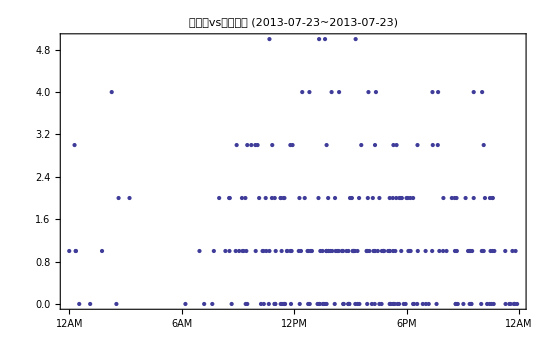

Export/AnsVSTime(2013-07-23~2013-07-23)2013-7-24-10.png

```mathematica
DateListPlot[Table[{DateList@resultS[[i,5]],resultS[[i,4]]},{i,1,totalQ}],PlotLabel->"回答数vs提问时间  ("<>condition1<>"~"<>condition2<>")",DateTicksFormat->{"Hour12Short","AMPM"}]
Export["Export/AnsVSTime("<>condition1<>"~"<>condition2<>")"<>ToString[First@Date[]]<>"-"<>ToString[Date[][[2]]]<>"-"<>ToString[Date[][[3]]]<>"-"<>ToString[Date[][[4]]]<>".png",%]
```

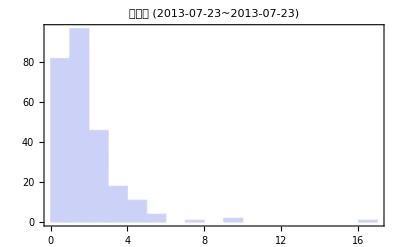

Export/AnsNumber-Histogram(2013-07-23~2013-07-23)2013-7-24-10.png

```mathematica
Histogram[Table[resultS[[i,4]],{i,1,totalQ}],Frame->True,PlotLabel->"回答数 ("<>condition1<>"~"<>condition2<>")"]
Export["Export/AnsNumber-Histogram("<>condition1<>"~"<>condition2<>")"<>ToString[First@Date[]]<>"-"<>ToString[Date[][[2]]]<>"-"<>ToString[Date[][[3]]]<>"-"<>ToString[Date[][[4]]]<>".png",%]
(*  SmoothHistogram@Table[resultS[[i,4]],{i,1,totalQ}]  *)
```

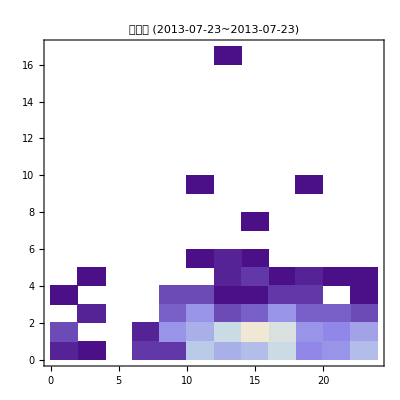

Export/QuestionTimeVSAnswerNumber(2013-07-23~2013-07-23)2013-7-24-10.png

```mathematica
DensityHistogram[Table[{First@Take[DateList@resultS[[i,5]],{4}],resultS[[i,4]]},{i,1,totalQ}],PlotLabel->"回答数 ("<>condition1<>"~"<>condition2<>")"]
Export["Export/QuestionTimeVSAnswerNumber("<>condition1<>"~"<>condition2<>")"<>ToString[First@Date[]]<>"-"<>ToString[Date[][[2]]]<>"-"<>ToString[Date[][[3]]]<>"-"<>ToString[Date[][[4]]]<>".png",%]
```

Vertical line is the # of answers in a question, horizontal line is the timestamp when the question is promoted.

The following functions can only be used for one day because I used the hour # of the day.

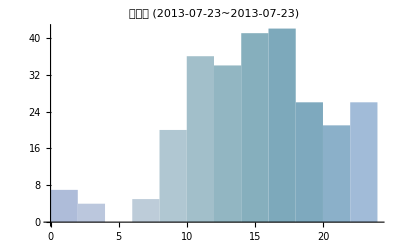

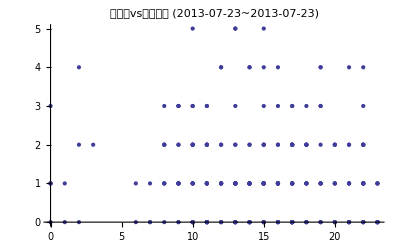

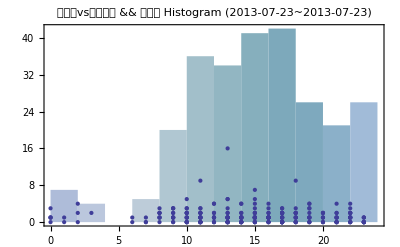

Export/HistoAndAnswerVSTime(2013-07-23~2013-07-23)2013-7-24-10.png

```mathematica
histo1=Histogram[Table[First@Take[DateList@resultS[[i,5]],{4}],{i,1,totalQ}],ChartBaseStyle->EdgeForm@None,ChartStyle->"Aquamarine",PlotLabel->"问题数 ("<>condition1<>"~"<>condition2<>")"]
listplt1=ListPlot[Table[{First@Take[DateList@resultS[[i,5]],{4}],resultS[[i,4]]},{i,1,totalQ}],PlotLabel->"回答数vs提问时间 ("<>condition1<>"~"<>condition2<>")"]
Show[histo1,listplt1,Frame->True,PlotLabel->"回答数vs提问时间 && 问题数 Histogram ("<>condition1<>"~"<>condition2<>")"]
Export["Export/HistoAndAnswerVSTime("<>condition1<>"~"<>condition2<>")"<>ToString[First@Date[]]<>"-"<>ToString[Date[][[2]]]<>"-"<>ToString[Date[][[3]]]<>"-"<>ToString[Date[][[4]]]<>".png",%]
```

## Using The ID of The Questions As Identity

The problem of previous methods is that the page id would change with time.

```mathematica
url2[s_,e_]:=Table[StringJoin["http://www.guokr.com/question/"<>ToString[i]],{i,s,e}]
```

```mathematica
urlList2=url2[482146,482665];
```

```mathematica
len2=Length@urlList2
```

520

## Draft

```mathematica
(*
XMLElement["li",{},{t1_,XMLElement["div",{"class"->"ask-list-nums"},{t2_,XMLElement["p",{"class"->"ask-focus-nums"},{t3_,XMLElement["span",{"class"->"num"},{focusN_}],focusNT_}],t4_,XMLElement["p",{"class"->"ask-answer-nums"},{t5_,XMLElement["span",{"class"->"num"},{ansN_}],ansNT_}],t6_}],t7_,XMLElement["div",{"class"->"ask-list-detials"},{t8_,XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->link_},{title_}]}],
t9_,XMLElement["div",{"class"->"ask-list-legend"},{t10_,XMLElement["p",{"class"->"ask-list-tags"},{labels_}],t11_,XMLElement["span",{"class"->"ask-list-time"},{time_}],t12_}],t13_}],
,t14_}]
*)
```

```mathematica
(*
XMLElement["li",{},{"\n        ",XMLElement["div",{"class"->"ask-list-nums"},{t7_,XMLElement["p",{"class"->"ask-focus-nums"},{"\n            ",XMLElement["span",{"class"->"num"},{"2"}],"关注\n            "}],"\n            ",XMLElement["p",{"class"->"ask-answer-nums"},{"\n            ",XMLElement["span",{"class"->"num"},{"1"}],"回答\n            "}],"\n            \n        "}],"\n        ",XMLElement["div",{"class"->"ask-list-detials"},{"\n            ",XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/question/482064/"},{"3D眩晕症的进阶问题，除了FPS晕。玩TPS也晕。黑道圣徒3.老滚（上古卷轴）。。玩老滚5直接给吐了。什么情况。怎么破\n"}]}],

"\\n            ",XMLElement["div",{"class"->"ask-list-legend"},{"\\n                ",XMLElement["p",{"class"->"ask-list-tags"},{"\\n                标签：\\n                \\n                \\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E5%A5%87%E6%80%9D%E5%A6%99%E6%83%B3%E9%97%AE%E9%A2%98/"},{"奇思妙想问题"}],"\\n                \\n                \\n                ",XMLElement["span",{"class"->"split"},{"|"}],"\\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E6%97%A0%E6%84%8F%E4%B9%89%E9%97%AE%E9%A2%98/"},{"无意义问题"}],"\\n                \\n                \\n                ",XMLElement["span",{"class"->"split"},{"|"}],"\\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E5%A5%87%E8%91%A9%E9%97%AE%E9%A2%98/"},{"奇葩问题"}],"\\n                \\n                \\n                "}],"\\n                ",XMLElement["span",{"class"->"ask-list-time"},{"\\n                    \\n                    \\n                    2013-07-06 01:01\\n                    \\n                "}],"\\n            "}],"\\n        "}],
*)
```

```mathematica
(*
XMLElement["a",{"shape"->"rect","class"->"gbtn-primary","id"->"newPost","href"->"/questions/new/","data-login"->"yes"},{"提问"}],"\\n    "}],"\\n    ",XMLElement["ul",{"class"->"ask-list"},{XMLElement["li",{},{"\\n        ",XMLElement["div",{"class"->"ask-list-nums"},{"\\n            ",XMLElement["p",{"class"->"ask-focus-nums"},{"\\n            ",XMLElement["span",{"class"->"num"},{"2"}],"关注\\n            "}],"\\n            ",XMLElement["p",{"class"->"ask-answer-nums"},{"\\n            ",XMLElement["span",{"class"->"num"},{"1"}],"回答\\n            "}],"\\n            \\n        "}],"\\n        ",XMLElement["div",{"class"->"ask-list-detials"},{"\\n            ",XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/question/482064/"},{"3D眩晕症的进阶问题，除了FPS晕。玩TPS也晕。黑道圣徒3.老滚（上古卷轴）。。玩老滚5直接给吐了。什么情况。怎么破\\n"}]}],"\\n            ",XMLElement["div",{"class"->"ask-list-legend"},{"\\n                ",XMLElement["p",{"class"->"ask-list-tags"},{"\\n                标签：\\n                \\n                \\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E5%A5%87%E6%80%9D%E5%A6%99%E6%83%B3%E9%97%AE%E9%A2%98/"},{"奇思妙想问题"}],"\\n                \\n                \\n                ",XMLElement["span",{"class"->"split"},{"|"}],"\\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E6%97%A0%E6%84%8F%E4%B9%89%E9%97%AE%E9%A2%98/"},{"无意义问题"}],"\\n                \\n                \\n                ",XMLElement["span",{"class"->"split"},{"|"}],"\\n                \\n                ",XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/ask/tag/%E5%A5%87%E8%91%A9%E9%97%AE%E9%A2%98/"},{"奇葩问题"}],"\\n                \\n                \\n                "}],"\\n                ",XMLElement["span",{"class"->"ask-list-time"},{"\\n                    \\n                    \\n                    2013-07-06 01:01\\n                    \\n                "}],"\\n            "}],"\\n        "}],
*)
```

```mathematica
(*
XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->"http://www.guokr.com/question/482064/"},{"3D眩晕症的进阶问题，除了FPS晕。玩TPS也晕。黑道圣徒3.老滚（上古卷轴）。。玩老滚5直接给吐了。什么情况。怎么破\\n"}]}]
*)
```

```mathematica
(*
XMLElement["div",{"class"->"ask-list-nums"},{"\\n            ",XMLElement["p",{"class"->"ask-focus-nums"},{"\\n            ",XMLElement["span",{"class"->"num"},{"2"}],"关注\\n            "}],"\\n            ",XMLElement["p",{"class"->"ask-answer-nums"},{"\\n            ",XMLElement["span",{"class"->"num"},{"1"}],"回答\\n            "}],"\\n            \\n        "}]
*)
```